## Plot Style

```mathematica
MyDarkOrange=RGBColor[255/255,127/255,14/255];
MyOrange=RGBColor[255/255,191/255,135/255];
MyDarkRed=RGBColor[214/255,39/255,40/255];
MyRed=RGBColor[236/255,146/255,147/255];
MyDarkBlue=RGBColor[31/255,119/255,180/255];
MyBlue=RGBColor[127/255,190/255,233/255];
MyDarkYellow=RGBColor[188/255,189/255,34/255];
MyYellow=RGBColor[233/255,234/255,133/255];
MyDarkGreen=RGBColor[45/255,160/255,45/255];
MyGreen=RGBColor[135/255,222/255,135/255];
MyDarkPink=RGBColor[227/255,120/255,194/255];
MyPink=RGBColor[241/255,187/255,225/255];
MyDarkPurple=RGBColor[148/255,103/255,189/255];
MyPurple=RGBColor[202/255,179/255,222/255];
```

```mathematica
MyFont="Times";
MyLabelSize=20;
MyTickSize=16;
MyLegendSize=12;
```

```mathematica
MyOptions=Sequence[
AspectRatio->1,
(*Axes->None,*)
Frame->True,
GridLinesStyle->Lighter[Lighter[Gray]],
LabelStyle->Directive[FontFamily->MyFont,FontSize->MyLabelSize],
FrameStyle->Directive[FontFamily->MyFont,FontSize->MyLabelSize],
FrameTicksStyle->Directive[FontFamily->MyFont,FontSize->MyTickSize],
ImageSize->450];
```

```mathematica
labeledTicks1=Table[{i,Style[Superscript[10,i],Black]},{i,-20,15}];
labeledTicks1=labeledTicks1/.{Style[Superscript[10,1],Black]->10,Style[Superscript[10,0],Black]->1,Style[Superscript[10,-1],Black]->0.1,Style[Superscript[10,-2],Black]->0.01};
unlabeledTicks1=Flatten[Table[{Log[k*j]/Log[10],Null},{k,2,9},{j,10^labeledTicks1[[All,1]]}],1];
myTicks1=Join[labeledTicks1,unlabeledTicks1];

labeledTicks2=Table[{i,Style[Superscript[10,i],Transparent]},{i,-20,15}];
labeledTicks2=labeledTicks2/.{Style[Superscript[10,1],Black]->10,Style[Superscript[10,0],Black]->1,Style[Superscript[10,-1],Black]->0.1,Style[Superscript[10,-2],Black]->0.01};
unlabeledTicks2=Flatten[Table[{Log[k*j]/Log[10],Null},{k,2,9},{j,10^labeledTicks2[[All,1]]}],1];
myTicks2=Join[labeledTicks2,unlabeledTicks2];

labeledTicksNegative1=Table[{-i,Style[-Superscript[10,i],Black]},{i,-20,15}];
labeledTicksNegative1=labeledTicksNegative1/.{Style[-Superscript[10,1],Black]->-10,Style[-Superscript[10,0],Black]->-1,Style[-Superscript[10,-1],Black]->-0.1,Style[-Superscript[10,-2],Black]->-0.01};
unlabeledTicksNegative1=Flatten[Table[{-Log[k*j]/Log[10],Null},{k,2,9},{j,10^labeledTicksNegative1[[All,1]]}],1];
myTicksNegative1=Join[labeledTicksNegative1,unlabeledTicksNegative1];

labeledTicksNegative2=Table[{-i,Style[-Superscript[10,i],Transparent]},{i,-20,15}];
labeledTicksNegative2=labeledTicksNegative2/.{Style[-Superscript[10,1],Black]->-10,Style[-Superscript[10,0],Black]->-1,Style[-Superscript[10,-1],Black]->-0.1,Style[-Superscript[10,-2],Black]->-0.01};
unlabeledTicksNegative2=Flatten[Table[{-Log[k*j]/Log[10],Null},{k,2,9},{j,10^labeledTicksNegative2[[All,1]]}],1];
myTicksNegative2=Join[labeledTicksNegative2,unlabeledTicksNegative2];
```

## Numerical Constants

```mathematica
GF=1.166*10^-5;
alpha=1/128.; (* at the EW scale *)
e=Sqrt[4*π*alpha]; (* at EW scale; enters the background prediction *)

Vcs=0.97;
Vts=0.04;
sW=Sqrt[0.231];
cW=Sqrt[1-sW^2];

v=246;

mZ=91.1876;deltamZ=0.0021;
mW=80.379;deltamW=0.012;
mh=125.25;deltamh=0.17;

mt=172.76;deltamt=0.3;
mc=1.27;deltamc=0.02;
mu=0.00216;deltamuplus=0.00049;deltamuminus=0.00026;

mb=4.18;deltambplus=0.03;deltambminus=0.02;
ms=0.93;deltamsplus=0.011;deltamsminus=0.005;
md=0.00467;deltamdplus=0.00048;deltamdminus=0.00017;

mtau=1.77686;deltamtau=0.00012;
mmu=0.1056583745;deltammu=0.0000000024;
me=0.0005109989461;deltame=0.0000000000031;

mpi=0.139;


(* translate units *)
(* 1/GeV^2 = 0.3894 10^12 fb *)
convert=0.3894*10^12;
```

```mathematica
(* 
from PDG 
hbar=6.582119569*10^-25; (* in GeV s *)
GF=1.1663788*10^-5; (* in GeV^-2 *)
alpha=1/127.951; (* alpha at MZ *)
e=Sqrt[4*π*alpha];

Vcs=0.97;
Vts=0.04;
sW=Sqrt[0.231];
cW=Sqrt[1-sW^2];

v=246;

mZ=91.1876;deltamZ=0.0021;
mW=80.379;deltamW=0.012;
mh=125.25;deltamh=0.17;

mt=172.76;deltamt=0.3;
mc=1.27;deltamc=0.02;
mu=0.00216;deltamuplus=0.00049;deltamuminus=0.00026;

mb=4.18;deltambplus=0.03;deltambminus=0.02;
ms=0.93;deltamsplus=0.011;deltamsminus=0.005;
md=0.00467;deltamdplus=0.00048;deltamdminus=0.00017;

mtau=1.77686;deltamtau=0.00012;
mmu=0.1056583745;deltammu=0.0000000024;
me=0.0005109989461;deltame=0.0000000000031;

mpi=0.139;
convert=0.3894*10^12;
*)
(*
(* masses in GeV *)
m$Z=91.1876;
m$W=80.377; (* PDG average that does not include the 2022 CDF and the 2023 ATLAS result; the precise value of mW has no impact on the numerics *)
sW2=0.23141; (* weak mixing angle at MZ; PDG calls this s_ND^2 *)
sW=Sqrt[sW2];
cW=Sqrt[1-sW2];

m$t$pole$mean=172.5; (* PDG average of the pole mass from cross section measurements (should be robust) *)
m$t$pole$delta=0.7;

m$t$MSbar$mean=162.92; (* MSbar value translated from the pole value above using 3-loop QCD *)
m$t$MSbar$delta=0.718;

m$t=m$t$MSbar$mean; (* use MSbar value *)
*)
```

```mathematica
(*
(* measured partial widths of the Z from LEP (in MeV) from table 7.1 of hep-ex/0509008 *)
GammaZhadexp=1745.8;deltaGammaZhad=2.7;
GammaZeeexp=83.92;deltaGammaZee=0.12;
GammaZmumuexp=83.99;deltaGammaZmumu=0.18;
GammaZtautauexp=84.08;deltaGammaZtautau=0.22;
GammaZbbexp=377.6;deltaGammaZbb=1.3;
GammaZccexp=300.5;deltaGammaZcc=5.3;
GammaZinvexp=497.4;deltaGammaZinv=2.5;
sigmaZ={deltaGammaZhad,deltaGammaZee,deltaGammaZmumu,deltaGammaZtautau,deltaGammaZbb,deltaGammaZcc,deltaGammaZinv};
(* correlation matrix from the same table *)
rhoZ={{1,-0.29,0.66,0.54,0.45,0.09,-0.67},{-0.29,1,-0.2,-0.17,-0.13,-0.02,0.78},{0.66,-0.2,1,0.39,0.29,0.06,-0.45},{0.54,-0.17,0.39,1,0.24,0.05,-0.4},{0.45,-0.13,0.29,0.24,1,-0.12,-0.3},{0.09,-0.02,0.06,0.05,-0.12,1,-0.06},{-0.67,0.78,-0.45,-0.4,-0.3,-0.06,1}};
(* construct the covariance matrix *)
CovZ=Table[sigmaZ[[ii]]*sigmaZ[[jj]]*rhoZ[[ii,jj]],{ii,1,7},{jj,1,7}];

(* SM predictions (in MeV) from table G.2 (left column) of hep-ex/0509008  (we ignore the uncertainties) *)
GammaSMZhad=1742.3;
GammaSMZee=83.987;
GammaSMZmumu=83.986;
GammaSMZtautau=83.796;
GammaSMZbb=376.02;
GammaSMZcc=300.1;
GammaSMZuu=300.16;
GammaSMZinv=501.62;
*)
```

## Top Branching Ratios

WG_Branching Ratios

```mathematica
BRtqll[Lambda_,ClltqLR_,ClltqRR_]:=1/96/π^2*mt^2*v^2/Lambda^4*(Abs[ClltqLR]^2+Abs[ClltqRR]^2)/(1-mW^2/mt^2)^2/(1+2*mW^2/mt^2);
BRtqllp[Lambda_,CllptqLR_,CllptqRR_,ClpltqLR_,ClpltqRR_]:=1/96/π^2*mt^2*v^2/Lambda^4*(Abs[CllptqLR]^2+Abs[CllptqRR]^2+Abs[ClpltqLR]^2+Abs[ClpltqRR]^2)/(1-mW^2/mt^2)^2/(1+2*mW^2/mt^2);
```

## Single Top Production

WG_ Single Top Production at LEP

```mathematica
sigmaeetq[s_][Lambda_,CeetqLR_,CeetqRR_]:=1/6/π*s/Lambda^4*(1-mt^2/s)^2*(1+mt^2/2/s)*(Abs[CeetqLR]^2+Abs[CeetqRR]^2)*convert;
```

## Di-Lepton Production

WG_Old Di-lepton Production at LHC

```mathematica
(* cross section in fb for mll > 2 TeV *)

sigmappll[Lambda_,ClluuLR_,ClluuRR_,CllccLR_,CllccRR_]:=Module[
{sigmaNPLRu1=-0.003309,
sigmaNPLRu2=0.020447,
sigmaNPRRu1=-0.015187,
sigmaNPRRu2=0.032325,
sigmaNPLRc1=-0.00003579,
sigmaNPLRc2=0.00017929,
sigmaNPRRc1=-0.00014333,
sigmaNPRRc2=0.00028682,
result},
result=(sigmaNPLRu1-sigmaNPLRu2)/2*10000^2/Lambda^2*ClluuLR+(sigmaNPLRu1+sigmaNPLRu2)/2*10000^4/Lambda^4*ClluuLR^2+(sigmaNPRRu1-sigmaNPRRu2)/2*10000^2/Lambda^2*ClluuRR+(sigmaNPRRu1+sigmaNPRRu2)/2*10000^4/Lambda^4*ClluuRR^2+(sigmaNPLRc1-sigmaNPLRc2)/2*10000^2/Lambda^2*CllccLR+(sigmaNPLRc1+sigmaNPLRc2)/2*10000^4/Lambda^4*CllccLR^2+(sigmaNPRRc1-sigmaNPRRc2)/2*10000^2/Lambda^2*CllccRR+(sigmaNPRRc1+sigmaNPRRc2)/2*10000^4/Lambda^4*CllccRR^2;
Return[result];]


(* bounds from ATLAS 2006.12946; Rll > 1 means excluded at 95% CL *)

Ree[Lambda_,CeeuuLR_,CeeuuRR_,CeeccLR_,CeeccRR_]:=Module[{Nsigedes=4.4,Nsigecon=16.0,Nbgedes=3.1,Nbgecon=12.4,sigmaSMedes=0.1751,sigmaSMecon=0.9891,result},result=Max[(-0.05298*CeeuuLR/Lambda^2*100+0.06554*CeeuuLR^2/Lambda^4*10000-0.10596*CeeuuRR/Lambda^2*100+0.06554*CeeuuRR^2/Lambda^4*10000-0.0003209*CeeccLR/Lambda^2*100+0.0003807*CeeccLR^2/Lambda^4*10000-0.0006418*CeeccRR/Lambda^2*100+0.00038074*CeeccRR^2/Lambda^4*10000)/sigmaSMedes*Nbgedes/Nsigedes,(-0.1925*CeeuuLR/Lambda^2*100+0.16225*CeeuuLR^2/Lambda^4*10000-0.38497*CeeuuRR/Lambda^2*100+0.16225*CeeuuRR^2/Lambda^4*10000-0.001548*CeeccLR/Lambda^2*100+0.001221*CeeccLR^2/Lambda^4*10000-0.003096*CeeccRR/Lambda^2*100+0.001221*CeeccRR^2/Lambda^4)/sigmaSMecon*Nbgecon/Nsigecon];
Return[result];]

Rmumu[Lambda_,CmumuuuLR_,CmumuuuRR_,CmumuccLR_,CmumuccRR_]:=Module[{Nsigmudes=3.8,Nsigmucon=5.8,Nbgmudes=1.4,Nbgmucon=9.6,sigmaSMmudes=0.3167,sigmaSMmucon=1.5018,result},result=Max[(-0.08297*CmumuuuLR/Lambda^2*100+0.090526*CmumuuuLR^2/Lambda^4*10000-0.16594*CmumuuuRR/Lambda^2*100+0.090526*CmumuuuRR^2/Lambda^4*10000-0.00054996*CmumuccLR/Lambda^2*100+0.00057135*CmumuccLR^2/Lambda^4*10000-0.0010999*CmumuccRR/Lambda^2*100+0.00057135*CmumuccRR^2/Lambda^4*10000)/sigmaSMmudes*Nbgmudes/Nsigmudes,(-0.26028*CmumuuuLR/Lambda^2*100+0.19845*CmumuuuLR^2/Lambda^4*10000-0.52056*CmumuuuRR/Lambda^2*100+0.19845*CmumuuuRR^2/Lambda^4*10000-0.0022622*CmumuccLR/Lambda^2*100+0.001602*CmumuccLR^2/Lambda^4*10000-0.0045244*CmumuccRR/Lambda^2*100+0.001602*CmumuccRR^2/Lambda^4*10000)/sigmaSMmucon*Nbgmucon/Nsigmucon];
Return[result];]
```

New_Di-Lepton Production

```mathematica
AsigmamaxeeccLR = 1/1.94127026457379^2
AsigmamineeccLR = -(1/1.9006354461039^2)
AsigmamaxeeccRR = 1/1.88061^2
AsigmamineeccRR = -(1/1.96194^2)

AsigmamaxmumuccLR = 1/2.17331^2
AsigmaminmumuccLR = -(1/2.23183)^2
AsigmamaxmumuccRR = 1/2.1398^2
AsigmaminmumuccRR = -(1/2.27694)^2

BsigmamaxeeccLR = 1/2.3017^2
BsigmamineeccLR = -(1/2.35023^2)
BsigmamaxeeccRR = 1/2.27779 ^ 2
BsigmamineeccRR = -(1/2.3749^2)

BsigmamaxmumuccLR = 1/2.17331^2
BsigmaminmumuccLR = -(1/2.23183)^2
BsigmamaxmumuccRR = 1/2.1398^2
BsigmaminmumuccRR = -(1/2.27694)^2
```

0.265355

-0.276823

0.28275

-0.259794

0.211717

-0.20076

0.218401

-0.192884

0.188757

-0.181042

0.19274

-0.1773

0.211717

-0.20076

0.218401

-0.192884

```mathematica
AsigmamaxeeuuLR = 1/5.27391^2
AsigmamineeuuLR = -(1/6.50217^2)
AsigmamaxeeuuRR = 1/4.769150928294321^2
AsigmamineeuuRR = -(1/7.190353834502111^2)

AsigmamaxmumuuuLR = 1/5.798186284547347^2
AsigmaminmumuuuLR = -(1/7.838387528383883)^2
AsigmamaxmumuuuRR = 1/5.044994638212678^2
AsigmaminmumuuuRR = -(1/9.008618307698281)^2

BsigmamaxeeuuLR = 1/6.156550180088765^2
BsigmamineeuuLR = -(1/7.546530569153025^2)
BsigmamaxeeuuRR = 1/5.581969326387885 ^ 2
BsigmamineeuuRR = -(1/8.323333830397322^2)

BsigmamaxmumuuuLR = 1/5.099007137036327^2
BsigmaminmumuuuLR = -(1/5.90658034220024)^2
BsigmamaxmumuuuRR = 1/4.744375934425716^2
BsigmaminmumuuuRR = -(1/6.348083654547727)^2
```

0.035953

-0.0236528

0.0439661

-0.0193419

0.0297451

-0.016276

0.0392897

-0.0123221

0.0263831

-0.0175592

0.0320941

-0.0144346

0.0384617

-0.0286634

0.0444265

-0.024815

## B decays

WG_Old_B_decay

```mathematica
C9e[Lambda_,CeettLR_,CeettRR_,CeectLR_,CeectRR_]:=(CeettRR+CeettLR+Vcs/Vts*mc/mt*(CeectRR+CeectLR))/4/sW^2*mt^2/4/mW^2*v^2/Lambda^2*Log[Lambda^2/mW^2];
C9mu[Lambda_,CmumuttLR_,CmumuttRR_,CmumuctLR_,CmumuctRR_]:=(CmumuttRR+CmumuttLR+Vcs/Vts*mc/mt*(CmumuctRR+CmumuctLR))/4/sW^2*mt^2/4/mW^2*v^2/Lambda^2*Log[Lambda^2/mW^2];
C10e[Lambda_,CeettLR_,CeettRR_,CeectLR_,CeectRR_]:=(CeettRR-CeettLR+Vcs/Vts*mc/mt*(CeectRR-CeectLR))/4/sW^2*mt^2/4/mW^2*v^2/Lambda^2*Log[Lambda^2/mW^2];
C10mu[Lambda_,CmumuttLR_,CmumuttRR_,CmumuctLR_,CmumuctRR_]:=(CmumuttRR-CmumuttLR+Vcs/Vts*mc/mt*(CmumuctRR-CmumuctLR))/4/sW^2*mt^2/4/mW^2*v^2/Lambda^2*Log[Lambda^2/mW^2];


Bmean={-0.69,0.4,-1.42,-0.71};
sigmaB={0.21,0.17,0.9,0.7};
rhoB={{1,0.03,0.1,-0.12},{0.03,1,-0.07,0.21},{0.1,-0.07,1,0.91},{-0.12,0.21,0.91,1}};

CovB=Table[0,{ii,4},{jj,4}];
For[ii=1,ii<5,ii++,For[jj=1,jj<5,jj++,
CovB[[ii,jj]]=rhoB[[ii,jj]]*sigmaB[[ii]]*sigmaB[[jj]];]];

chi2Bdecay[Lambda_,CeettLR_,CeettRR_,CeectLR_,CeectRR_,CmumuttLR_,CmumuttRR_,CmumuctLR_,CmumuctRR_]:=Module[{C9ee,C10ee,C9mumu,C10mumu,result},
C9ee=C9e[Lambda,CeettLR,CeettRR,CeectLR,CeectRR];
C9mumu=C9mu[Lambda,CmumuttLR,CmumuttRR,CmumuctLR,CmumuctRR];
C10ee=C10e[Lambda,CeettLR,CeettRR,CeectLR,CeectRR];
C10mumu=C10mu[Lambda,CmumuttLR,CmumuttRR,CmumuctLR,CmumuctRR];
result=(Bmean-{C9mumu,C10mumu,C9ee,C10ee}).Inverse[CovB].(Bmean-{C9mumu,C10mumu,C9ee,C10ee});
Return[result];];
```

New_B_decay

```mathematica
COVmm={{.33^2,.87*.33*.22},{.87*.33*.22,.22^2}};
COVee={{.67^2,.977*.67*.73},{.977*.67*.73,.73^2}};
v=246;mt=172.5;mw=80.377;mc=1.27;sw2=.2314;mz=91.1876;
Vcs = .97;
Vts = .04;
fac=1/(4sw2)*mt^2/(4*mw^2)*v^2;
C9[CRRlltt_,CLRlltt_,CRRllct_,CLRllct_,Λ_  ]:=(CRRlltt+CLRlltt+(Vcs*mc/(Vts*mt))*(CRRllct+CLRllct))*fac*Log[Λ^2/mw^2]/Λ^2;
C10[CRRlltt_,CLRlltt_,CRRllct_,CLRllct_,Λ_]:=(CRRlltt-CLRlltt+(Vcs*mc/(Vts*mt))*(CRRllct-CLRllct))*fac*Log[Λ^2/mw^2]/Λ^2;
Cvecmm[CRRlltt_,CLRlltt_,CRRllct_,CLRllct_,Λ_  ]:={C9[CRRlltt,CLRlltt,CRRllct, CLRllct,Λ]+.26,C10[CRRlltt,CLRlltt,CRRllct, CLRllct,Λ]+.06};
Cvecee[CRRlltt_,CLRlltt_,CRRllct_,CLRllct_,Λ_]:={C9[CRRlltt,CLRlltt,CRRllct, CLRllct,Λ]-.61,C10[CRRlltt,CLRlltt,CRRllct, CLRllct,Λ]-.43};
χ2mm[CRRlltt_,CLRlltt_,CRRllct_,CLRllct_,Λ_]:=Cvecmm[CRRlltt,CLRlltt,CRRllct, CLRllct,Λ].Inverse[COVmm].Cvecmm[CRRlltt,CLRlltt,CRRllct, CLRllct,Λ];
χ2ee[CRRlltt_,CLRlltt_,CRRllct_,CLRllct_,Λ_]:=Cvecee[CRRlltt,CLRlltt,CRRllct, CLRllct,Λ].Inverse[COVee].Cvecee[CRRlltt,CLRlltt,CRRllct, CLRllct,Λ];
chisqrBdecay[Lambda_,CeettLR_,CeettRR_,CeectLR_,CeectRR_,CmumuttLR_,CmumuttRR_,CmumuctLR_,CmumuctRR_]:=
	χ2ee[CeettLR,CeettRR,CeectLR,CeectRR,Lambda]+χ2mm[CmumuttLR,CmumuttRR,CmumuctLR,CmumuctRR,Lambda];
```

## Z decays

WG_Old_Z_decay

```mathematica
RZll[Lambda_,CllttLR_,CllttRR_,CllccLR_,CllccRR_,ClluuLR_,ClluuRR_]:=1+((1-2*sW^2)*CllttLR-2*sW^2*CllttRR)/(1-4*sW^2+8*sW^4)*(3/4/π^2*mt^2/Lambda^2-sW^2/3/π^2*mZ^2/Lambda^2)*Log[Lambda^2/mt^2]+((2*sW^2-1)*(ClluuLR+CllccLR)+2*sW^2*(ClluuRR+CllccRR))/(1-4*sW^2+8*sW^4)*sW^2/3/π^2*mZ^2/Lambda^2*Log[Lambda^2/mZ^2];

RZnunu[Lambda_,CeettLR_,CmumuttLR_,CeeccLR_,CmumuccLR_,CeeuuLR_,CmumuuuLR_]:=1-1/3*(CeettLR+CmumuttLR)*(3/4/π^2*mt^2/Lambda^2-sW^2/3/π^2*mZ^2/Lambda^2)*Log[Lambda^2/mt^2]+1/3*(CeeuuLR+CmumuuuLR+CeeccLR+CmumuccLR)*sW^2/3/π^2*mZ^2/Lambda^2*Log[Lambda^2/mZ^2];

RZqq[Lambda_,CeeqqLR_,CeeqqRR_,CmumuqqLR_,CmumuqqRR_]:=1+sW^2/π^2*mZ^2/Lambda^2*Log[Lambda^2/mZ^2]*((sW^2-1)*(CeeqqLR+CmumuqqLR)+2*sW^2*(CeeqqRR+CmumuqqRR))/(9-24*sW^2+32*sW^4);
```

```mathematica
(* measured partial widths of the Z from LEP (in MeV) *)

GammaZhadexp=1745.8;deltaGammaZhad=2.7;
GammaZeeexp=83.92;deltaGammaZee=0.12;
GammaZmumuexp=83.99;deltaGammaZmumu=0.18;
GammaZtautauexp=84.08;deltaGammaZtautau=0.22;
GammaZbbexp=377.6;deltaGammaZbb=1.3;
GammaZccexp=300.5;deltaGammaZcc=5.3;
GammaZinvexp=497.4;deltaGammaZinv=2.5;

sigmaZ={deltaGammaZhad,deltaGammaZee,deltaGammaZmumu,deltaGammaZtautau,deltaGammaZbb,deltaGammaZcc,deltaGammaZinv};

GammaSMZhad=1742.3;
GammaSMZee=83.987;
GammaSMZmumu=83.986;
GammaSMZtautau=83.796;
GammaSMZbb=376.02;
GammaSMZcc=300.1;
GammaSMZuu=300.16;
GammaSMZinv=501.62;

rhoZ={{1,-0.29,0.66,0.54,0.45,0.09,-0.67},{-0.29,1,-0.2,-0.17,-0.13,-0.02,0.78},{0.66,-0.2,1,0.39,0.29,0.06,-0.45},{0.54,-0.17,0.39,1,0.24,0.05,-0.4},{0.45,-0.13,0.29,0.24,1,-0.12,-0.3},{0.09,-0.02,0.06,0.05,-0.12,1,-0.06},{-0.67,0.78,-0.45,-0.4,-0.3,-0.06,1}};

CovZ=Table[0,{ii,7},{jj,7}];
For[ii=1,ii<8,ii++,For[jj=1,jj<8,jj++,
CovZ[[ii,jj]]=sigmaZ[[ii]]*sigmaZ[[jj]]*rhoZ[[ii,jj]];]];

chi2Zdecay[Lambda_,CeettLR_,CmumuttLR_,CeeccLR_,CmumuccLR_,CeeuuLR_,CmumuuuLR_,CeettRR_,CmumuttRR_,CeeccRR_,CmumuccRR_,CeeuuRR_,CmumuuuRR_]:=Module[{GammaZhad,GammaZee,GammaZmumu,GammaZcc,GammaZinv,result},
GammaZinv=GammaSMZinv*RZnunu[Lambda,CeettLR,CmumuttLR,CeeccLR,CmumuccLR,CeeuuLR,CmumuuuLR];
GammaZee=GammaSMZee*RZll[Lambda,CeettLR,CeettRR,CeeccLR,CeeccRR,CeeuuLR,CeeuuRR];
GammaZmumu=GammaSMZmumu*RZll[Lambda,CmumuttLR,CmumuttRR,CmumuccLR,CmumuccRR,CmumuuuLR,CmumuuuRR];
GammaZcc=GammaSMZcc*RZqq[Lambda,CeeccLR,CeeccRR,CmumuccLR,CmumuccRR];GammaZhad=GammaSMZhad+GammaSMZcc*(RZqq[Lambda,CeeccLR,CeeccRR,CmumuccLR,CmumuccRR]-1)+GammaSMZuu*(RZqq[Lambda,CeeuuLR,CeeuuRR,CmumuuuLR,CmumuuuRR]-1);

result=({GammaZhadexp,GammaZeeexp,GammaZmumuexp,GammaZtautauexp,GammaZbbexp,GammaZccexp,GammaZinvexp}-{GammaZhad,GammaZee,GammaZmumu,GammaSMZtautau,GammaSMZbb,GammaZcc,GammaZinv}).Inverse[CovZ].({GammaZhadexp,GammaZeeexp,GammaZmumuexp,GammaZtautauexp,GammaZbbexp,GammaZccexp,GammaZinvexp}-{GammaZhad,GammaZee,GammaZmumu,GammaSMZtautau,GammaSMZbb,GammaZcc,GammaZinv});

Return[result];];

minZdecay=chi2Zdecay[L,0,0,0,0,0,0,0,0,0,0,0,0];
```

New_Z_Decay

```mathematica
M1=({{0, 0, 0, 0, 0, 0, 0}, {-.29*2.7*.12, 0, 0, 0, 0, 0, 0}, {.66*2.7*.18, -.2*.12*.18, 0, 0, 0, 0, 0}, {.54*2.7*.22, -.17*.12*.22, .39*.18*.22, 0, 0, 0, 0}, {0.45*2.7*1.3, -0.13*.12*1.3, 0.29*.18*1.3, 0.24*.22*1.3, 0, 0, 0}, {0.09*2.7*5.3, -0.02*.12*5.3, 0.06*.18*5.3, 0.05*.22*5.3, -0.12*1.3*5.3, 0, 0}, {-0.67*2.7*2.5, 0.78*.12*2.5, -0.45*.18*2.5, -0.4*.22*2.5, -0.3*1.3*2.5, -0.06*5.3*2.5, 0}});M2={{2.7^2,0,0,0,0,0,0},{0,.12^2,0,0,0,0,0},{0,0,.18^2,0,0,0,0},{0,0,0,.22^2,0,0,0},{0,0,0,0,1.3^2,0,0},{0,0,0,0,0,5.3^2,0},{0,0,0,0,0,0,2.5^2}}
COV=10^(-12)*(M1+Transpose[M1]+M2);
v=246;mt=162.92;mw=80.377;mc=1.27;sw2=.23141;sw=Sqrt[sw2];mz=91.1876;
Γll[ΓSM_,CllttLR_,CllttRR_,ClluuLR_,ClluuRR_,CllccLR_,CllccRR_,Λ_]:=ΓSM*(1+((1-2*sw^2)*CllttLR-2*sw^2*CllttRR)/(1-4*sw^2+8*sw^4)*((3*mt^2)/(4*Pi^2*Λ^2)-(sw^2*mz^2)/(3*Pi^2*Λ^2))*Log[Λ^2/mt^2]+(((2*sw^2-1)*(ClluuLR+CllccLR)+2*sw^2*(ClluuRR+CllccRR))/(1-4*sw2+8*sw^4))*sw^2/(3*Pi^2)*mz^2/Λ^2*Log[Λ^2/mz^2]);
Γνν[ΓSM_,CeettLR_,CμμttLR_,CeeuuLR_,CμμuuLR_,CeeccLR_,CμμccLR_,Λ_]:=ΓSM*(1-1/3*(CeettLR+CμμttLR)*(3/(4*Pi^2)*mt^2/Λ^2-sw2/(3*Pi^2)*mz^2/Λ^2)*Log[Λ^2/mt^2]+1/3*(CeeuuLR+CμμuuLR+CeeccLR+CμμccLR)*sw2/(3*Pi^2)*mz^2/Λ^2*Log[Λ^2/mz^2]);
Γqq[ΓSM_,CeeqqLR_,CμμqqLR_,CeeqqRR_,CμμqqRR_,Λ_]:=ΓSM*(1+sw^2/π^2*mz^2/Λ^2*Log[Λ^2/mz^2]*(((2*sw^2-1)*(CeeqqLR+CμμqqLR)+2*sw2*(CeeqqRR+CμμqqRR))/(9-24*sw^2+32*sw^4)));
xhadron[CeettLR_,CeettRR_,CeeuuLR_,CeeuuRR_,CeeccLR_,CeeccRR_,CμμttLR_,CμμttRR_,CμμuuLR_,CμμuuRR_,CμμccLR_,CμμccRR_,Λ_]:=1745.8*10^(-6)-1.7423*10^(-3)-.30016*10^(-3)*(Γqq[1,CeeuuLR,CμμuuLR,CeeuuRR,CμμuuRR,Λ]-1)-.30010*10^(-3)*(Γqq[1,CeeccLR,CμμccLR,CeeccRR,CμμccRR,Λ]-1);
xee[CeettLR_,CeettRR_,CeeuuLR_,CeeuuRR_,CeeccLR_,CeeccRR_,CμμttLR_,CμμttRR_,Λ_]:=.08392*10^(-3)-Γll[.083987*10^(-3),CeettLR,CeettRR,CeeuuLR,CeeuuRR,CeeccLR,CeeccRR,Λ];
xμμ[CμμttLR_,CμμttRR_,CμμuuLR_,CμμuuRR_,CμμccLR_,CμμccRR_,Λ_]:=.08399*10^(-3)-Γll[.083986*10^(-3),CμμttLR,CμμttRR,CμμuuLR,CμμuuRR,CμμccLR,CμμccRR,Λ];
xττ[CeettLR_,CeettRR_,CeeuuLR_,CeeuuRR_,CeeccLR_,CeeccRR_,CμμttLR_,CμμttRR_,Λ_]:=(.08408-.083796)*10^(-3);
xbb[CeettLR_,CeettRR_,CeeuuLR_,CeeuuRR_,CeeccLR_,CeeccRR_,CμμttLR_,
CμμttRR_,Λ_]:=(.3776-.37602)*10^(-3);
xcc[CeettLR_,CeettRR_,CeeuuLR_,CeeuuRR_,CeeccLR_,CeeccRR_,CμμttLR_,CμμttRR_,CμμccLR_,CμμccRR_,Λ_]:=.3005*10^(-3)-Γqq[.30010*10^(-3),CeeccLR,CμμccLR,CeeccRR,CμμccRR,Λ];
xinv[CeettLR_,CeettRR_,CeeuuLR_,CeeuuRR_,CeeccLR_,CeeccRR_,CμμttLR_,CμμttRR_,CμμuuLR_,CμμccLR_,Λ_]:=.4974*10^(-3)-Γνν[.50162*10^(-3),CeettLR,CμμttLR,CeeuuLR,CμμuuLR,CeeccLR,CμμccLR,Λ];
Γvec[CeettLR_,CeettRR_,CeeuuLR_,CeeuuRR_,CeeccLR_,CeeccRR_,CμμttLR_,CμμttRR_,CμμccLR_,CμμccRR_,CμμuuLR_,CμμuuRR_,Λ_]:={xhadron[CeettLR,CeettRR,CeeuuLR,CeeuuRR,CeeccLR,CeeccRR,CμμttLR,CμμttRR,CμμuuLR,CμμuuRR,CμμccLR,CμμccRR,Λ],xee[CeettLR,CeettRR,CeeuuLR,CeeuuRR,CeeccLR,CeeccRR,CμμttLR,CμμttRR,Λ],xμμ[CμμttLR,CμμttRR,CμμuuLR,CμμuuRR,CμμccLR,CμμccRR,Λ],xττ[CeettLR,CeettRR,CeeuuLR,CeeuuRR,CeeccLR,CeeccRR,CμμttLR,CμμttRR,Λ],xbb[CeettLR,CeettRR,CeeuuLR,CeeuuRR,CeeccLR,CeeccRR,CμμttLR,CμμttRR,Λ],xcc[CeettLR,CeettRR,CeeuuLR,CeeuuRR,CeeccLR,CeeccRR,CμμttLR,CμμttRR,CμμccLR,CμμccRR,Λ],
xinv[CeettLR,CeettRR,CeeuuLR,CeeuuRR,CeeccLR,CeeccRR,CμμttLR,CμμttRR,CμμuuLR,CμμccLR,Λ]};
χ2[CeettLR_,CeettRR_,CeeuuLR_,CeeuuRR_,CeeccLR_,CeeccRR_,CμμttLR_,CμμttRR_,CμμccLR_,CμμccRR_,CμμuuLR_,CμμuuRR_,Λ_]:=Γvec[CeettLR,CeettRR,CeeuuLR,CeeuuRR,CeeccLR,CeeccRR,CμμttLR,CμμttRR,CμμccLR,CμμccRR,CμμuuLR,CμμuuRR,Λ].Inverse[COV].Γvec[CeettLR,CeettRR,CeeuuLR,CeeuuRR,CeeccLR,CeeccRR,CμμttLR,CμμttRR,CμμccLR,CμμccRR,CμμuuLR,CμμuuRR,Λ];
```

{{7.29,0,0,0,0,0,0},{0,0.0144,0,0,0,0,0},{0,0,0.0324,0,0,0,0},{0,0,0,0.0484,0,0,0},{0,0,0,0,1.69,0,0},{0,0,0,0,0,28.09,0},{0,0,0,0,0,0,6.25}}

```mathematica
minZdecay=χ2[0,0,0,0,0,0,0,0,0,0,0,0,L];
```

## Plots CeectLR, CeeccLR, CeettLR

```mathematica
L=1000;
minBdecayPos=NMinimize[{chisqrBdecay[L,C1,0,C2,0,0,0,0,0],C1>0},{C1,C2}][[1]];
minBdecayNeg=NMinimize[{chisqrBdecay[L,C1,0,C2,0,0,0,0,0],C1<0},{C1,C2}][[1]];

maxCeeccLR=AsigmamaxeeccLR;
minCeeccLR=AsigmamineeccLR;

ppttllLRPosPos = RegionPlot[10^C1 >2.39*Sqrt[2], {C1, Log[0.005]/Log[10], Log[6]/Log[10]}, {C2,Log[0.005]/Log[10],Log[20]/Log[10]}, BoundaryStyle->Directive[Black,Thick],PlotStyle->Directive[Lighter@Purple, Opacity[0.5]]];
```

```mathematica
(*maxCeettLR=NMaximize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pMollerPosPos2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerPosPos1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

maxCeettLR=NMaximize[{C1,χ2[C1,0,0,0,C3,0,0,0,0,0,0,0,L]-minZdecay<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pZdecayPosPos2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayPosPos1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayPosPos1=RegionPlot[chisqrBdecay[L,10^C1,0,10^C2,0,0,0,0,0]-minBdecayPos>4,{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
(*pBdecayPosPos2=RegionPlot[chisqrBdecay[L,10^C1,0,10^C2,0,0,0,0,0]-minBdecayPos>1,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];*)
pBdecayPosPos3=ContourPlot[chisqrBdecay[L,10^C1,0,10^C2,0,0,0,0,0]-minBdecayPos,{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopPosPos2=ContourPlot[sigmaeetq[189^2][L,10^C2,0],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopPosPos1=RegionPlot[sigmaeetq[189^2][L,10^C2,0]>110,{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,Log[1]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopPosPos2=ContourPlot[BRtqll[L,10^C2,0],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,Log[0.5]/Log[10],Log[20]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopPosPos1=RegionPlot[BRtqll[L,10^C2,0]>2.1*10^-4,{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopPosPos3=ContourPlot[BRtqll[L,10^C2,0],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryPosPos1=RegionPlot[10^C2>Sqrt[maxCeeccLR*10^C1],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryPosPos2=ContourPlot[10^C2==Sqrt[maxCeeccLR/2*10^C1],{C1,Log[0.006]/Log[10],Log[maxCeettLR]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

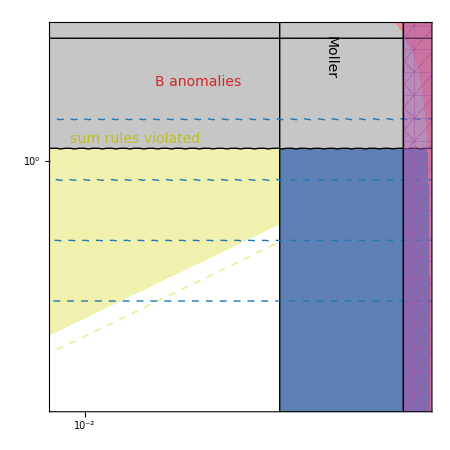

```mathematica
plotTR=Show[ptheoryPosPos1,ptheoryPosPos2,(*pMollerPosPos1,*)pZdecayPosPos1,psingletopPosPos1,praretopPosPos1,(*pMollerPosPos2,*)pBdecayPosPos1,(*pBdecayPosPos2,*)pZdecayPosPos2,psingletopPosPos2,praretopPosPos2,praretopPosPos3,pBdecayPosPos3,ppttllLRPosPos,Evaluate[MyOptions],PlotRange->Log[{{0.006,5},{0.01,12}}]/Log[10],FrameTicks->{{myTicks2,None},{myTicks2,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"","","UV scalar dominated"},
Epilog->{Text[Style["B anomalies",FontFamily->MyFont,FontSize->14,MyDarkRed],{-1.1,.65},Automatic,{1,-0.05}],
Text[Style["Moller",FontFamily->MyFont,FontSize->14,Black],{-0.05,.85},Automatic,{0,-1}],
Text[Style["sum rules violated",FontFamily->MyFont,FontSize->14,MyDarkYellow],{-1.6,.18},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

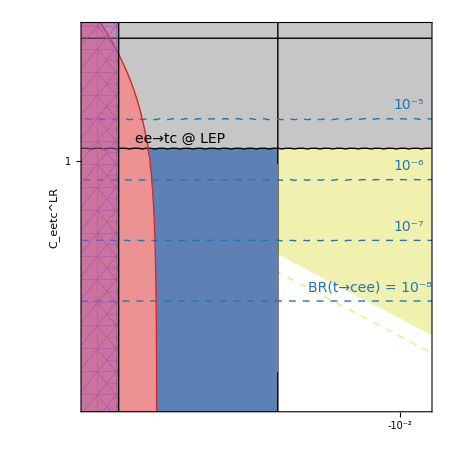

```mathematica
(*minCeettLR=NMinimize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pMollerNegPos2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerNegPos1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

ppttllLRNegPos = RegionPlot[10^-C1 >1.91*Sqrt[2], {C1, -Log[0.005]/Log[10], -Log[6]/Log[10]}, {C2,Log[0.005]/Log[10],Log[20]/Log[10]}, BoundaryStyle->Directive[Black,Thick],PlotStyle->Directive[Lighter@Purple, Opacity[0.5]]];

minCeettLR=NMinimize[{C1,χ2[C1,0,0,0,C3,0,0,0,0,0,0,0,L]-minZdecay<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pZdecayNegPos2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayNegPos1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayNegPos1=RegionPlot[chisqrBdecay[L,-10^-C1,0,10^C2,0,0,0,0,0]-minBdecayNeg>4,{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayNegPos2=RegionPlot[chisqrBdecay[L,-10^-C1,0,10^C2,0,0,0,0,0]-minBdecayNeg>1,{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed, Opacity[0.5]]];
pBdecayNegPos3=ContourPlot[chisqrBdecay[L,-10^-C1,0,10^C2,0,0,0,0,0]-minBdecayNeg,{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopNegPos2=ContourPlot[sigmaeetq[189^2][L,10^C2,0],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopNegPos1=RegionPlot[sigmaeetq[189^2][L,10^C2,0]>110,{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[1]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopNegPos2=ContourPlot[BRtqll[L,10^C2,0],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.5]/Log[10],Log[20]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopNegPos1=RegionPlot[BRtqll[L,10^C2,0]>2.1*10^-4,{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopNegPos3=ContourPlot[BRtqll[L,10^C2,0],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryNegPos1=RegionPlot[10^C2>Sqrt[maxCeeccLR*10^-C1],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryNegPos2=ContourPlot[10^C2==Sqrt[maxCeeccLR/2*10^-C1],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotTL=Show[ptheoryNegPos1,ptheoryNegPos2,(*pMollerNegPos1,*)pZdecayNegPos1,psingletopNegPos1,praretopNegPos1,(*pMollerNegPos2,*)pBdecayNegPos1,(*pBdecayNegPos2,*)pZdecayNegPos2,psingletopNegPos2,praretopNegPos2,praretopNegPos3,pBdecayNegPos3,ppttllLRNegPos,Evaluate[MyOptions],PlotRange->{-Log[{5,0.006}]/Log[10],Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicks1,None},{myTicksNegative2,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"","C_eetc^LR","UV vector dominated"},
Epilog->{Text[Style["BR(t→cee) = 10^-8",FontFamily->MyFont,FontSize->14,MyDarkBlue],{1.74,-1.04},Automatic,{1,0}],
Text[Style["10^-7",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-0.54},Automatic,{1,0}],
Text[Style["10^-6",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-.04},Automatic,{1,0}],
Text[Style["10^-5",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,.46},Automatic,{1,0}],
Text[Style["ee→tc @ LEP",FontFamily->MyFont,FontSize->14,Black],{.1,.18},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

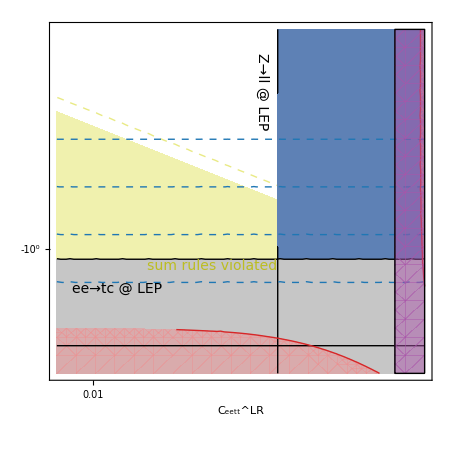

```mathematica
(*maxCeettLR=NMaximize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pMollerPosNeg2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerPosNeg1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

ppttllLRPosNeg = RegionPlot[10^C1 >2.39*Sqrt[2], {C1, Log[0.005]/Log[10], Log[6]/Log[10]}, {C2,-Log[0.005]/Log[10],-Log[20]/Log[10]}, BoundaryStyle->Directive[Black,Thick],PlotStyle->Directive[Lighter@Purple, Opacity[0.5]]];

maxCeettLR=NMaximize[{C1,χ2[C1,0,0,0,C3,0,0,0,0,0,0,0,L]-minZdecay<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pZdecayPosNeg2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayPosNeg1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayPosNeg1=RegionPlot[chisqrBdecay[L,10^C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg>4,{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayPosNeg2=RegionPlot[chisqrBdecay[L,10^C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg>1,{C1,Log[0.05]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayPosNeg3=ContourPlot[chisqrBdecay[L,10^C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg,{C1,Log[0.05]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopPosNeg2=ContourPlot[sigmaeetq[189^2][L,-10^-C2,0],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopPosNeg1=RegionPlot[sigmaeetq[189^2][L,-10^-C2,0]>110,{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopPosNeg2=ContourPlot[BRtqll[L,-10^-C2,0],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.5]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopPosNeg1=RegionPlot[BRtqll[L,-10^-C2,0]>2.1*10^-4,{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopPosNeg3=ContourPlot[BRtqll[L,-10^-C2,0],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryPosNeg1=RegionPlot[10^-C2>Sqrt[maxCeeccLR*10^C1],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryPosNeg2=ContourPlot[10^-C2==Sqrt[maxCeeccLR/2*10^C1],{C1,Log[0.005]/Log[10], Log[6]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotBR=Show[ptheoryPosNeg1,ptheoryPosNeg2,(*pMollerPosNeg1,*)pZdecayPosNeg1,psingletopPosNeg1,praretopPosNeg1,(*pMollerPosNeg2,*)pBdecayPosNeg1,(*pBdecayPosNeg2,*)pZdecayPosNeg2,psingletopPosNeg2,praretopPosNeg2,praretopPosNeg3,pBdecayPosNeg3,ppttllLRPosNeg,Evaluate[MyOptions],PlotRange->{Log[{0.006,5}]/Log[10],-Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicksNegative2,None},{myTicks1,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"C_eett^LR","",""},
Epilog->{Text[Style["Z→ll @ LEP",FontFamily->MyFont,FontSize->14,Black],{-0.58,1.65},Automatic,{0,-1}],
Text[Style["sum rules violated",FontFamily->MyFont,FontSize->14,MyDarkYellow],{-1.,-.18},Automatic,{1,0}],
Text[Style["ee→tc @ LEP",FontFamily->MyFont,FontSize->14,Black],{-1.8,-.42},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

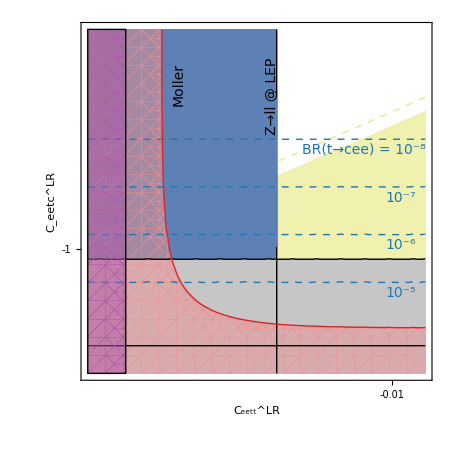

```mathematica
(*minCeettLR=NMinimize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pMollerNegNeg2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerNegNeg1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

ppttllLRNegNeg = RegionPlot[10^-C1 >1.91*Sqrt[2], {C1, -Log[0.005]/Log[10], -Log[6]/Log[10]}, {C2,-Log[0.005]/Log[10],-Log[20]/Log[10]}, BoundaryStyle->Directive[Black,Thick],PlotStyle->Directive[Lighter@Purple, Opacity[0.5]]];

minCeettLR=NMinimize[{C1,χ2[C1,0,0,0,C3,0,0,0,0,0,0,0,L]-minZdecay<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pZdecayNegNeg2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayNegNeg1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayNegNeg1=RegionPlot[chisqrBdecay[L,-10^-C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg>4,{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayNegNeg2=RegionPlot[chisqrBdecay[L,-10^-C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg>1,{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayNegNeg3=ContourPlot[chisqrBdecay[L,-10^-C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg,{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopNegNeg2=ContourPlot[sigmaeetq[189^2][L,-10^-C2,0],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopNegNeg1=RegionPlot[sigmaeetq[189^2][L,-10^-C2,0]>110,{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopNegNeg2=ContourPlot[BRtqll[L,-10^-C2,0],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.5]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopNegNeg1=RegionPlot[BRtqll[L,-10^-C2,0]>2.1*10^-4,{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopNegNeg3=ContourPlot[BRtqll[L,-10^-C2,0],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]]; 

ptheoryNegNeg1=RegionPlot[10^-C2>Sqrt[maxCeeccLR*10^-C1],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryNegNeg2=ContourPlot[10^-C2==Sqrt[maxCeeccLR/2*10^-C1],{C1,-Log[6]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotBL=Show[ptheoryNegNeg1,ptheoryNegNeg2,(*pMollerNegNeg1,*)pZdecayNegNeg1,psingletopNegNeg1,praretopNegNeg1,(*pMollerNegNeg2,*)pBdecayNegNeg1,(*pBdecayNegNeg2,*)pZdecayNegNeg2,psingletopNegNeg2,praretopNegNeg2,praretopNegNeg3,pBdecayNegNeg3,ppttllLRNegNeg,Evaluate[MyOptions],PlotRange->{-Log[{5,0.006}]/Log[10],-Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicksNegative1,None},{myTicksNegative1,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"C_eett^LR","C_eetc^LR",""},
Epilog->{Text[Style["BR(t→cee) = 10^-8",FontFamily->MyFont,FontSize->14,MyDarkBlue],{1.74,1.04},Automatic,{1,0}],
Text[Style["10^-7",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,0.54},Automatic,{1,0}],
Text[Style["10^-6",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,.04},Automatic,{1,0}],
Text[Style["10^-5",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-.46},Automatic,{1,0}],
Text[Style["Z→ll @ LEP",FontFamily->MyFont,FontSize->14,Black],{0.9,1.6},Automatic,{0,1}],
Text[Style["Moller",FontFamily->MyFont,FontSize->14,Black],{0.05,1.72},Automatic,{0,1}]}]
```

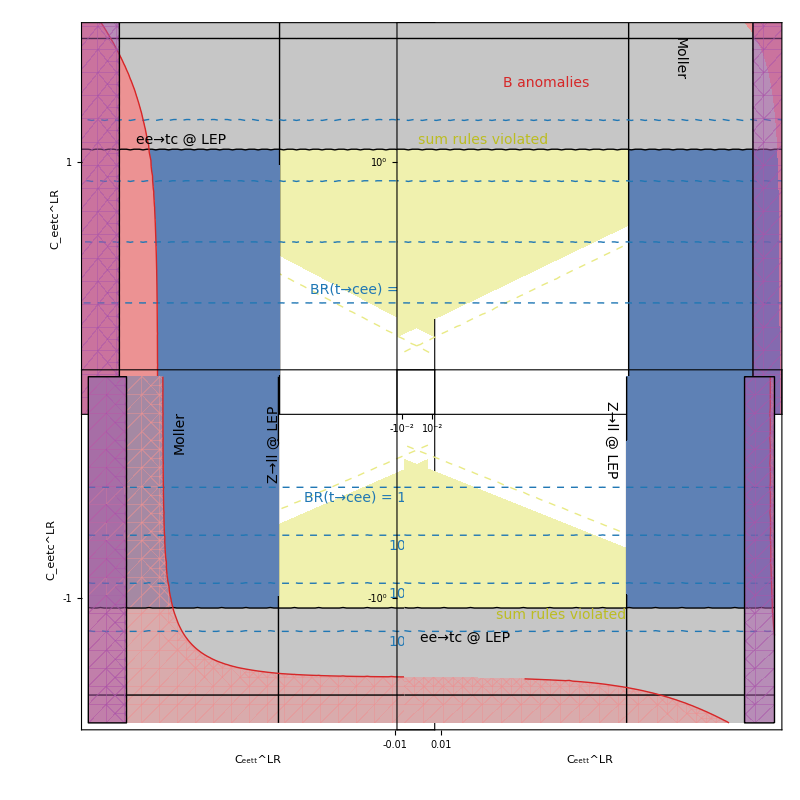

```mathematica
finalAeetcLR=GraphicsGrid[{{plotTL,plotTR},{plotBL,plotBR}},Spacings->{-105,-105},Frame->None,ImageSize->800]
```

```mathematica
L=1000;
minBdecayPos=NMinimize[{chisqrBdecay[L,C1,0,C2,0,0,0,0,0],C1>0},{C1,C2}][[1]];
minBdecayNeg=NMinimize[{chisqrBdecay[L,C1,0,C2,0,0,0,0,0],C1<0},{C1,C2}][[1]];

maxCeeccLR=BsigmamaxeeccLR;
minCeeccLR=BsigmamineeccLR;
```

```mathematica
(*maxCeettLR=NMaximize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pMollerPosPos2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerPosPos1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

maxCeettLR=NMaximize[{C1,χ2[C1,0,0,0,C3,0,0,0,0,0,0,0,L]-minZdecay<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pZdecayPosPos2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayPosPos1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayPosPos1=RegionPlot[chisqrBdecay[L,10^C1,0,10^C2,0,0,0,0,0]-minBdecayPos>4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayPosPos2=RegionPlot[chisqrBdecay[L,10^C1,0,10^C2,0,0,0,0,0]-minBdecayPos<1,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayPosPos3=ContourPlot[chisqrBdecay[L,10^C1,0,10^C2,0,0,0,0,0]-minBdecayPos,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopPosPos2=ContourPlot[sigmaeetq[189^2][L,10^C2,0],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopPosPos1=RegionPlot[sigmaeetq[189^2][L,10^C2,0]>110,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[1]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopPosPos2=ContourPlot[BRtqll[L,10^C2,0],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.5]/Log[10],Log[20]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopPosPos1=RegionPlot[BRtqll[L,10^C2,0]>2.1*10^-4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopPosPos3=ContourPlot[BRtqll[L,10^C2,0],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryPosPos1=RegionPlot[10^C2>Sqrt[maxCeeccLR*10^C1],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryPosPos2=ContourPlot[10^C2==Sqrt[maxCeeccLR/2*10^C1],{C1,Log[0.005]/Log[10],Log[maxCeettLR]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

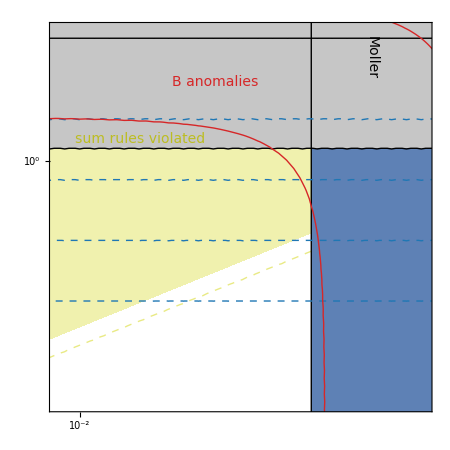

```mathematica
plotTR=Show[ptheoryPosPos1,ptheoryPosPos2,(*pMollerPosPos1,*)pZdecayPosPos1,psingletopPosPos1,praretopPosPos1,(*pMollerPosPos2,*)pBdecayPosPos1,(*pBdecayPosPos2,*)pZdecayPosPos2,psingletopPosPos2,praretopPosPos2,praretopPosPos3,pBdecayPosPos3,Evaluate[MyOptions],PlotRange->Log[{{0.007,2},{0.01,12}}]/Log[10],FrameTicks->{{myTicks2,None},{myTicks2,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"","","UV scalar dominated"},
Epilog->{Text[Style["B anomalies",FontFamily->MyFont,FontSize->14,MyDarkRed],{-1.1,.65},Automatic,{1,-0.05}],
Text[Style["Moller",FontFamily->MyFont,FontSize->14,Black],{-0.05,.85},Automatic,{0,-1}],
Text[Style["sum rules violated",FontFamily->MyFont,FontSize->14,MyDarkYellow],{-1.6,.18},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

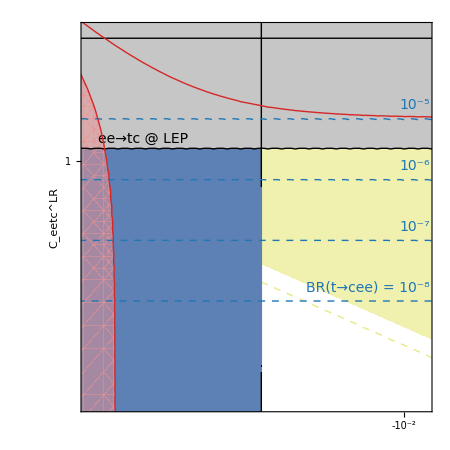

```mathematica
(*minCeettLR=NMinimize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pMollerNegPos2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerNegPos1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

minCeettLR=NMinimize[{C1,χ2[C1,0,0,0,C3,0,0,0,0,0,0,0,L]-minZdecay<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pZdecayNegPos2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayNegPos1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayNegPos1=RegionPlot[chisqrBdecay[L,-10^-C1,0,10^C2,0,0,0,0,0]-minBdecayNeg>4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayNegPos2=RegionPlot[chisqrBdecay[L,-10^-C1,0,10^C2,0,0,0,0,0]-minBdecayNeg<1,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayNegPos3=ContourPlot[chisqrBdecay[L,-10^-C1,0,10^C2,0,0,0,0,0]-minBdecayNeg,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopNegPos2=ContourPlot[sigmaeetq[189^2][L,10^C2,0],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopNegPos1=RegionPlot[sigmaeetq[189^2][L,10^C2,0]>110,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[1]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopNegPos2=ContourPlot[BRtqll[L,10^C2,0],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.5]/Log[10],Log[20]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopNegPos1=RegionPlot[BRtqll[L,10^C2,0]>2.1*10^-4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopNegPos3=ContourPlot[BRtqll[L,10^C2,0],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryNegPos1=RegionPlot[10^C2>Sqrt[maxCeeccLR*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryNegPos2=ContourPlot[10^C2==Sqrt[maxCeeccLR/2*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotTL=Show[ptheoryNegPos1,ptheoryNegPos2,(*pMollerNegPos1,*)pZdecayNegPos1,psingletopNegPos1,praretopNegPos1,(*pMollerNegPos2,*)pBdecayNegPos1,(*pBdecayNegPos2,*)pZdecayNegPos2,psingletopNegPos2,praretopNegPos2,praretopNegPos3,pBdecayNegPos3,Evaluate[MyOptions],PlotRange->{-Log[{2,0.007}]/Log[10],Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicks1,None},{myTicksNegative2,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"","C_eetc^LR","UV vector dominated"},
Epilog->{Text[Style["BR(t→cee) = 10^-8",FontFamily->MyFont,FontSize->14,MyDarkBlue],{1.74,-1.04},Automatic,{1,0}],
Text[Style["10^-7",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-0.54},Automatic,{1,0}],
Text[Style["10^-6",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-.04},Automatic,{1,0}],
Text[Style["10^-5",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,.46},Automatic,{1,0}],
Text[Style["ee→tc @ LEP",FontFamily->MyFont,FontSize->14,Black],{.1,.18},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

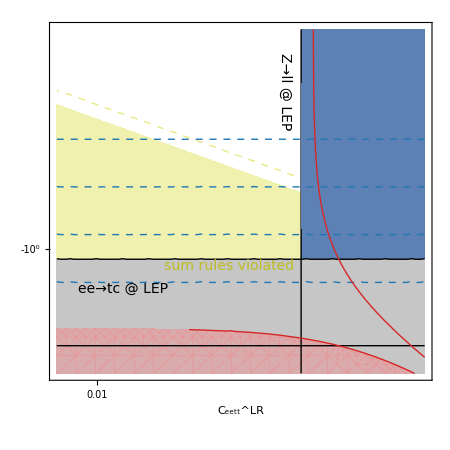

```mathematica
(*maxCeettLR=NMaximize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pMollerPosNeg2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerPosNeg1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

maxCeettLR=NMaximize[{C1,χ2[C1,0,0,0,C3,0,0,0,0,0,0,0,L]-minZdecay<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pZdecayPosNeg2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayPosNeg1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayPosNeg1=RegionPlot[chisqrBdecay[L,10^C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg>4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayPosNeg2=RegionPlot[chisqrBdecay[L,10^C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg<1,{C1,Log[0.05]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayPosNeg3=ContourPlot[chisqrBdecay[L,10^C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg,{C1,Log[0.05]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopPosNeg2=ContourPlot[sigmaeetq[189^2][L,-10^-C2,0],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopPosNeg1=RegionPlot[sigmaeetq[189^2][L,-10^-C2,0]>110,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopPosNeg2=ContourPlot[BRtqll[L,-10^-C2,0],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.5]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopPosNeg1=RegionPlot[BRtqll[L,-10^-C2,0]>2.1*10^-4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopPosNeg3=ContourPlot[BRtqll[L,-10^-C2,0],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryPosNeg1=RegionPlot[10^-C2>Sqrt[maxCeeccLR*10^C1],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryPosNeg2=ContourPlot[10^-C2==Sqrt[maxCeeccLR/2*10^C1],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotBR=Show[ptheoryPosNeg1,ptheoryPosNeg2,(*pMollerPosNeg1,*)pZdecayPosNeg1,psingletopPosNeg1,praretopPosNeg1,(*pMollerPosNeg2,*)pBdecayPosNeg1,(*pBdecayPosNeg2,*)pZdecayPosNeg2,psingletopPosNeg2,praretopPosNeg2,praretopPosNeg3,pBdecayPosNeg3,Evaluate[MyOptions],PlotRange->{Log[{0.007,2}]/Log[10],-Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicksNegative2,None},{myTicks1,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"C_eett^LR","",""},
Epilog->{Text[Style["Z→ll @ LEP",FontFamily->MyFont,FontSize->14,Black],{-0.58,1.65},Automatic,{0,-1}],
Text[Style["sum rules violated",FontFamily->MyFont,FontSize->14,MyDarkYellow],{-1.,-.18},Automatic,{1,0}],
Text[Style["ee→tc @ LEP",FontFamily->MyFont,FontSize->14,Black],{-1.8,-.42},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

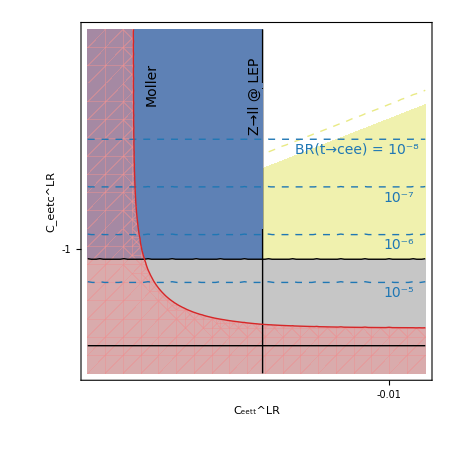

```mathematica
(*minCeettLR=NMinimize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pMollerNegNeg2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerNegNeg1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

minCeettLR=NMinimize[{C1,χ2[C1,0,0,0,C3,0,0,0,0,0,0,0,L]-minZdecay<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pZdecayNegNeg2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayNegNeg1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayNegNeg1=RegionPlot[chisqrBdecay[L,-10^-C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg>4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayNegNeg2=RegionPlot[chisqrBdecay[L,-10^-C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg<1,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayNegNeg3=ContourPlot[chisqrBdecay[L,-10^-C1,0,-10^-C2,0,0,0,0,0]-minBdecayNeg,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopNegNeg2=ContourPlot[sigmaeetq[189^2][L,-10^-C2,0],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopNegNeg1=RegionPlot[sigmaeetq[189^2][L,-10^-C2,0]>110,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopNegNeg2=ContourPlot[BRtqll[L,-10^-C2,0],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.5]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopNegNeg1=RegionPlot[BRtqll[L,-10^-C2,0]>2.1*10^-4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopNegNeg3=ContourPlot[BRtqll[L,-10^-C2,0],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]]; 

ptheoryNegNeg1=RegionPlot[10^-C2>Sqrt[maxCeeccLR*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryNegNeg2=ContourPlot[10^-C2==Sqrt[maxCeeccLR/2*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotBL=Show[ptheoryNegNeg1,ptheoryNegNeg2,(*pMollerNegNeg1,*)pZdecayNegNeg1,psingletopNegNeg1,praretopNegNeg1,(*pMollerNegNeg2,*)pBdecayNegNeg1,(*pBdecayNegNeg2,*)pZdecayNegNeg2,psingletopNegNeg2,praretopNegNeg2,praretopNegNeg3,pBdecayNegNeg3,Evaluate[MyOptions],PlotRange->{-Log[{2,0.007}]/Log[10],-Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicksNegative1,None},{myTicksNegative1,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"C_eett^LR","C_eetc^LR",""},
Epilog->{Text[Style["BR(t→cee) = 10^-8",FontFamily->MyFont,FontSize->14,MyDarkBlue],{1.74,1.04},Automatic,{1,0}],
Text[Style["10^-7",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,0.54},Automatic,{1,0}],
Text[Style["10^-6",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,.04},Automatic,{1,0}],
Text[Style["10^-5",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-.46},Automatic,{1,0}],
Text[Style["Z→ll @ LEP",FontFamily->MyFont,FontSize->14,Black],{0.9,1.6},Automatic,{0,1}],
Text[Style["Moller",FontFamily->MyFont,FontSize->14,Black],{0.05,1.72},Automatic,{0,1}]}]
```

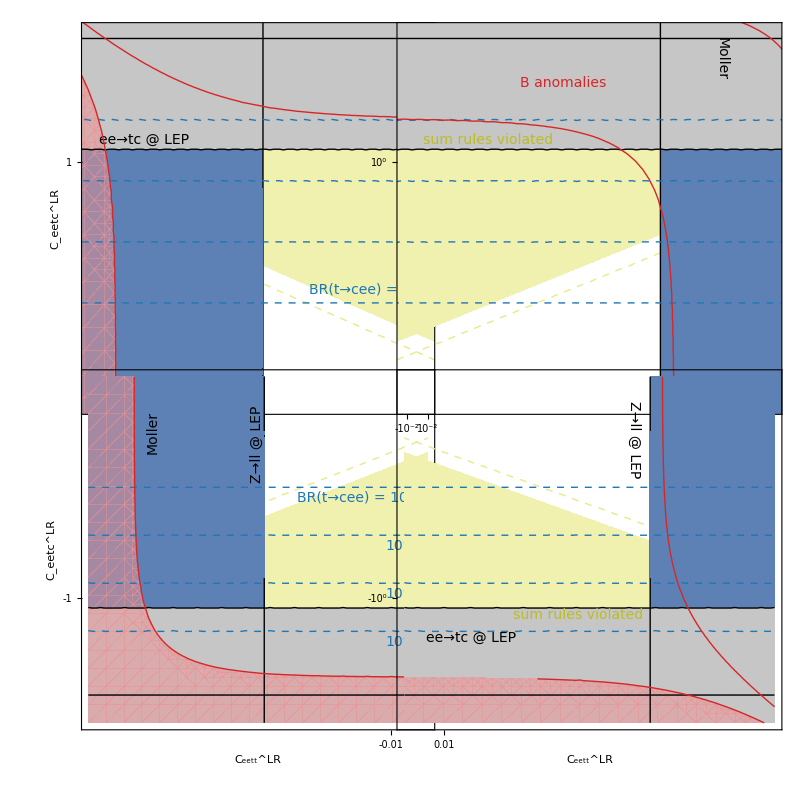

```mathematica
finalBeetcLR=GraphicsGrid[{{plotTL,plotTR},{plotBL,plotBR}},Spacings->{-105,-105},Frame->None,ImageSize->800]
```

## Plots CeectRR, CeeccRR, CeettRR

```mathematica
L=1000;
minBdecayPos=NMinimize[{chisqrBdecay[L,0,C1,0,C2,0,0,0,0],C1>0},{C1,C2}][[1]];
minBdecayNeg=NMinimize[{chisqrBdecay[L,0,C1,0,C2,0,0,0,0],C1<0},{C1,C2}][[1]];

maxCeeccRR=AsigmamaxeeccRR;
minCeeccRR=AsigmamineeccRR;
```

```mathematica
(*maxCeettLR=NMaximize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pMollerPosPos2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerPosPos1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

maxCeettRR=NMaximize[{C1,χ2[0,C1,0,0,0,C3,0,0,0,0,0,0,L]-minZdecay<4,0<C3<maxCeeccRR},{C1,C3}][[1]];
pZdecayPosPos2=ContourPlot[C1==Log[maxCeettRR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayPosPos1=RegionPlot[C1>Log[maxCeettRR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayPosPos1=RegionPlot[chisqrBdecay[L,0,10^C1,0,10^C2,0,0,0,0]-minBdecayPos>4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayPosPos2=RegionPlot[chisqrBdecay[L,0,10^C1,0,10^C2,0,0,0,0]-minBdecayPos<1,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayPosPos3=ContourPlot[chisqrBdecay[L,0,10^C1,0,10^C2,0,0,0,0]-minBdecayPos,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopPosPos2=ContourPlot[sigmaeetq[189^2][L,0,10^C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopPosPos1=RegionPlot[sigmaeetq[189^2][L,0,10^C2]>110,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[1]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopPosPos2=ContourPlot[BRtqll[L,0,10^C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.5]/Log[10],Log[20]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopPosPos1=RegionPlot[BRtqll[L,0,10^C2]>2.1*10^-4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopPosPos3=ContourPlot[BRtqll[L,0,10^C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryPosPos1=RegionPlot[10^C2>Sqrt[maxCeeccRR*10^C1],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryPosPos2=ContourPlot[10^C2==Sqrt[maxCeeccRR/2*10^C1],{C1,Log[0.005]/Log[10],Log[maxCeettRR]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

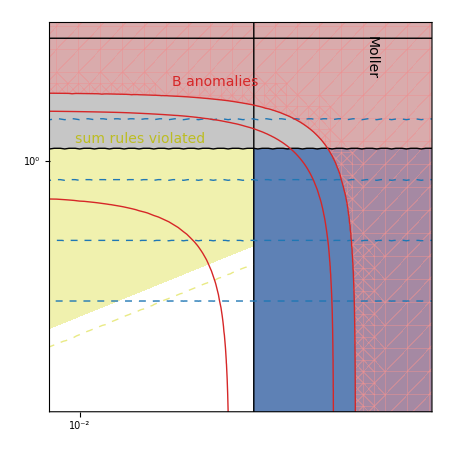

```mathematica
plotTR=Show[ptheoryPosPos1,ptheoryPosPos2,(*pMollerPosPos1,*)pZdecayPosPos1,psingletopPosPos1,praretopPosPos1,(*pMollerPosPos2,*)pBdecayPosPos1,(*pBdecayPosPos2,*)pZdecayPosPos2,psingletopPosPos2,praretopPosPos2,praretopPosPos3,pBdecayPosPos3,Evaluate[MyOptions],PlotRange->Log[{{0.007,2},{0.01,12}}]/Log[10],FrameTicks->{{myTicks2,None},{myTicks2,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"","","UV scalar dominated"},
Epilog->{Text[Style["B anomalies",FontFamily->MyFont,FontSize->14,MyDarkRed],{-1.1,.65},Automatic,{1,-0.05}],
Text[Style["Moller",FontFamily->MyFont,FontSize->14,Black],{-0.05,.85},Automatic,{0,-1}],
Text[Style["sum rules violated",FontFamily->MyFont,FontSize->14,MyDarkYellow],{-1.6,.18},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

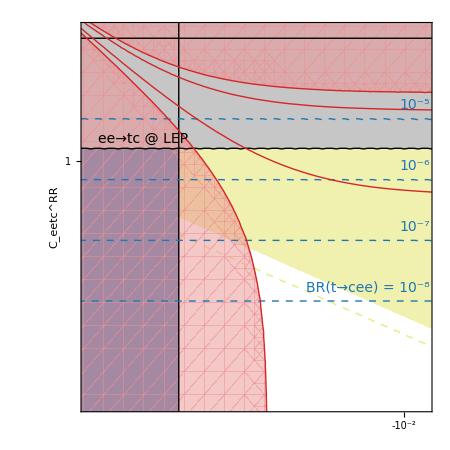

```mathematica
(*minCeettLR=NMinimize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pMollerNegPos2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerNegPos1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

minCeettRR=NMinimize[{C1,χ2[0,C1,0,0,0,C3,0,0,0,0,0,0,L]-minZdecay<4,minCeeccRR<C3<0},{C1,C3}][[1]];
pZdecayNegPos2=ContourPlot[C1==-Log[-minCeettRR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayNegPos1=RegionPlot[C1<-Log[-minCeettRR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayNegPos1=RegionPlot[chisqrBdecay[L,0,-10^-C1,0,10^C2,0,0,0,0]-minBdecayNeg>4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayNegPos2=RegionPlot[chisqrBdecay[L,0,-10^-C1,0,10^C2,0,0,0,0]-minBdecayNeg<1,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayNegPos3=ContourPlot[chisqrBdecay[L,0,-10^-C1,0,10^C2,0,0,0,0]-minBdecayNeg,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopNegPos2=ContourPlot[sigmaeetq[189^2][L,0,10^C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopNegPos1=RegionPlot[sigmaeetq[189^2][L,0,10^C2]>110,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[1]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopNegPos2=ContourPlot[BRtqll[L,0,10^C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.5]/Log[10],Log[20]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopNegPos1=RegionPlot[BRtqll[L,0,10^C2]>2.1*10^-4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopNegPos3=ContourPlot[BRtqll[L,0,10^C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryNegPos1=RegionPlot[10^C2>Sqrt[maxCeeccRR*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryNegPos2=ContourPlot[10^C2==Sqrt[maxCeeccRR/2*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotTL=Show[ptheoryNegPos1,ptheoryNegPos2,(*pMollerNegPos1,*)pZdecayNegPos1,psingletopNegPos1,praretopNegPos1,(*pMollerNegPos2,*)pBdecayNegPos1,(*pBdecayNegPos2,*)pZdecayNegPos2,psingletopNegPos2,praretopNegPos2,praretopNegPos3,pBdecayNegPos3,Evaluate[MyOptions],PlotRange->{-Log[{2,0.007}]/Log[10],Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicks1,None},{myTicksNegative2,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"","C_eetc^RR","UV vector dominated"},
Epilog->{Text[Style["BR(t→cee) = 10^-8",FontFamily->MyFont,FontSize->14,MyDarkBlue],{1.74,-1.04},Automatic,{1,0}],
Text[Style["10^-7",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-0.54},Automatic,{1,0}],
Text[Style["10^-6",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-.04},Automatic,{1,0}],
Text[Style["10^-5",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,.46},Automatic,{1,0}],
Text[Style["ee→tc @ LEP",FontFamily->MyFont,FontSize->14,Black],{.1,.18},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

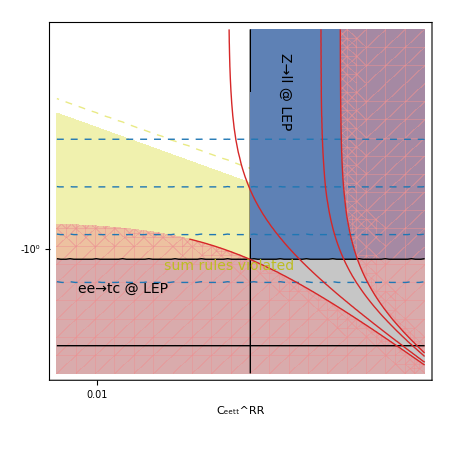

```mathematica
(*maxCeettLR=NMaximize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pMollerPosNeg2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerPosNeg1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

maxCeettRR=NMaximize[{C1,χ2[0,C1,0,0,0,C3,0,0,0,0,0,0,L]-minZdecay<4,0<C3<maxCeeccRR},{C1,C3}][[1]];
pZdecayPosNeg2=ContourPlot[C1==Log[maxCeettRR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayPosNeg1=RegionPlot[C1>Log[maxCeettRR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayPosNeg1=RegionPlot[chisqrBdecay[L,0,10^C1,0,-10^-C2,0,0,0,0]-minBdecayNeg>4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayPosNeg2=RegionPlot[chisqrBdecay[L,0,10^C1,0,-10^-C2,0,0,0,0]-minBdecayNeg<1,{C1,Log[0.05]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayPosNeg3=ContourPlot[chisqrBdecay[L,0,10^C1,0,-10^-C2,0,0,0,0]-minBdecayNeg,{C1,Log[0.05]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopPosNeg2=ContourPlot[sigmaeetq[189^2][L,0,-10^-C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopPosNeg1=RegionPlot[sigmaeetq[189^2][L,0,-10^-C2]>110,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopPosNeg2=ContourPlot[BRtqll[L,0,-10^-C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.5]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopPosNeg1=RegionPlot[BRtqll[L,0,-10^-C2]>2.1*10^-4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopPosNeg3=ContourPlot[BRtqll[L,0,-10^-C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryPosNeg1=RegionPlot[10^-C2>Sqrt[maxCeeccRR*10^C1],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryPosNeg2=ContourPlot[10^-C2==Sqrt[maxCeeccRR/2*10^C1],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotBR=Show[ptheoryPosNeg1,ptheoryPosNeg2,(*pMollerPosNeg1,*)pZdecayPosNeg1,psingletopPosNeg1,praretopPosNeg1,(*pMollerPosNeg2,*)pBdecayPosNeg1,(*pBdecayPosNeg2,*)pZdecayPosNeg2,psingletopPosNeg2,praretopPosNeg2,praretopPosNeg3,pBdecayPosNeg3,Evaluate[MyOptions],PlotRange->{Log[{0.007,2}]/Log[10],-Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicksNegative2,None},{myTicks1,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"C_eett^RR","",""},
Epilog->{Text[Style["Z→ll @ LEP",FontFamily->MyFont,FontSize->14,Black],{-0.58,1.65},Automatic,{0,-1}],
Text[Style["sum rules violated",FontFamily->MyFont,FontSize->14,MyDarkYellow],{-1.,-.18},Automatic,{1,0}],
Text[Style["ee→tc @ LEP",FontFamily->MyFont,FontSize->14,Black],{-1.8,-.42},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

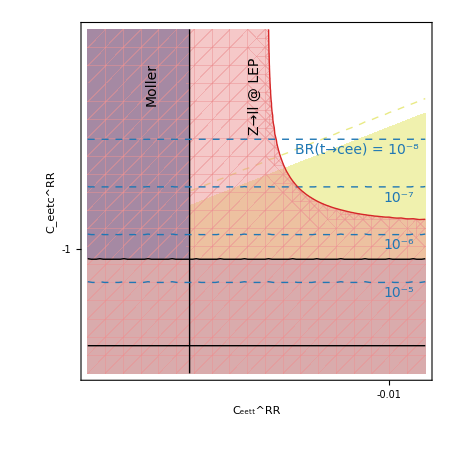

```mathematica
(*minCeettLR=NMinimize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pMollerNegNeg2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerNegNeg1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

minCeettRR=NMinimize[{C1,χ2[0,C1,0,0,0,C3,0,0,0,0,0,0,L]-minZdecay<4,minCeeccRR<C3<0},{C1,C3}][[1]];
pZdecayNegNeg2=ContourPlot[C1==-Log[-minCeettRR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayNegNeg1=RegionPlot[C1<-Log[-minCeettRR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayNegNeg1=RegionPlot[chisqrBdecay[L,0,-10^-C1,0,-10^-C2,0,0,0,0]-minBdecayNeg>4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayNegNeg2=RegionPlot[chisqrBdecay[L,0,-10^-C1,0,-10^-C2,0,0,0,0]-minBdecayNeg<1,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayNegNeg3=ContourPlot[chisqrBdecay[L,0,-10^-C1,0,-10^-C2,0,0,0,0]-minBdecayNeg,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopNegNeg2=ContourPlot[sigmaeetq[189^2][L,0,-10^-C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopNegNeg1=RegionPlot[sigmaeetq[189^2][L,0,-10^-C2]>110,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopNegNeg2=ContourPlot[BRtqll[L,0,-10^-C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.5]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopNegNeg1=RegionPlot[BRtqll[L,0,-10^-C2]>2.1*10^-4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopNegNeg3=ContourPlot[BRtqll[L,0,-10^-C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]]; 

ptheoryNegNeg1=RegionPlot[10^-C2>Sqrt[maxCeeccRR*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryNegNeg2=ContourPlot[10^-C2==Sqrt[maxCeeccRR/2*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotBL=Show[ptheoryNegNeg1,ptheoryNegNeg2,(*pMollerNegNeg1,*)pZdecayNegNeg1,psingletopNegNeg1,praretopNegNeg1,(*pMollerNegNeg2,*)pBdecayNegNeg1,(*pBdecayNegNeg2,*)pZdecayNegNeg2,psingletopNegNeg2,praretopNegNeg2,praretopNegNeg3,pBdecayNegNeg3,Evaluate[MyOptions],PlotRange->{-Log[{2,0.007}]/Log[10],-Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicksNegative1,None},{myTicksNegative1,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"C_eett^RR","C_eetc^RR",""},
Epilog->{Text[Style["BR(t→cee) = 10^-8",FontFamily->MyFont,FontSize->14,MyDarkBlue],{1.74,1.04},Automatic,{1,0}],
Text[Style["10^-7",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,0.54},Automatic,{1,0}],
Text[Style["10^-6",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,.04},Automatic,{1,0}],
Text[Style["10^-5",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-.46},Automatic,{1,0}],
Text[Style["Z→ll @ LEP",FontFamily->MyFont,FontSize->14,Black],{0.9,1.6},Automatic,{0,1}],
Text[Style["Moller",FontFamily->MyFont,FontSize->14,Black],{0.05,1.72},Automatic,{0,1}]}]
```

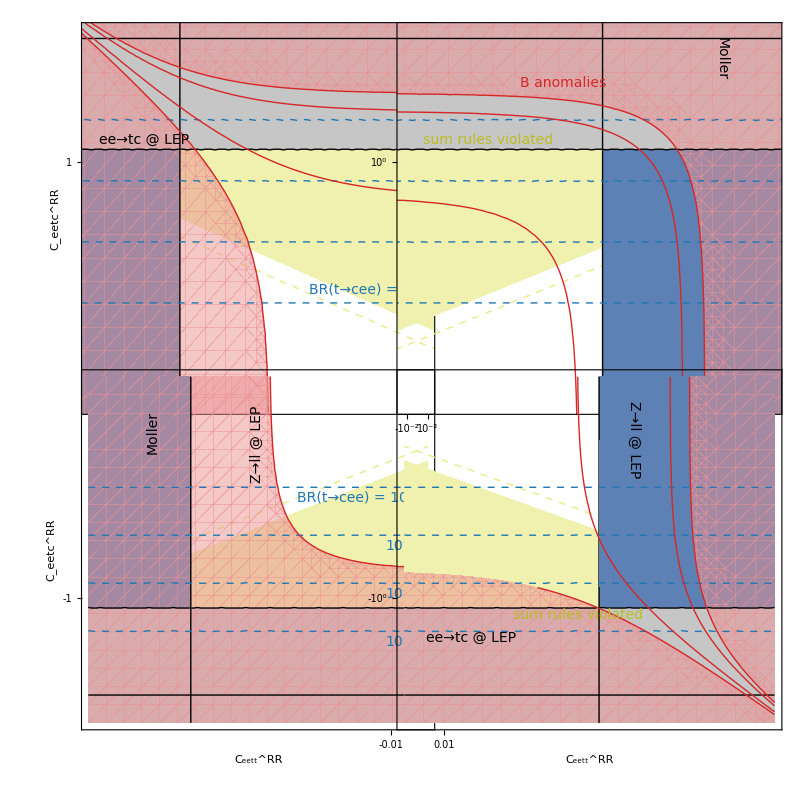

```mathematica
finalAeetcRR=GraphicsGrid[{{plotTL,plotTR},{plotBL,plotBR}},Spacings->{-105,-105},Frame->None,ImageSize->800]
```

```mathematica
L=1000;
minBdecayPos=NMinimize[{chisqrBdecay[L,0,C1,0,C2,0,0,0,0],C1>0},{C1,C2}][[1]];
minBdecayNeg=NMinimize[{chisqrBdecay[L,0,C1,0,C2,0,0,0,0],C1<0},{C1,C2}][[1]];

maxCeeccRR=BsigmamaxeeccRR;
minCeeccRR=BsigmamineeccRR;
```

```mathematica
(*maxCeettLR=NMaximize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pMollerPosPos2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerPosPos1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

maxCeettRR=NMaximize[{C1,χ2[0,C1,0,0,0,C3,0,0,0,0,0,0,L]-minZdecay<4,0<C3<maxCeeccRR},{C1,C3}][[1]];
pZdecayPosPos2=ContourPlot[C1==Log[maxCeettRR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayPosPos1=RegionPlot[C1>Log[maxCeettRR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayPosPos1=RegionPlot[chisqrBdecay[L,0,10^C1,0,10^C2,0,0,0,0]-minBdecayPos>4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayPosPos2=RegionPlot[chisqrBdecay[L,0,10^C1,0,10^C2,0,0,0,0]-minBdecayPos<1,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayPosPos3=ContourPlot[chisqrBdecay[L,0,10^C1,0,10^C2,0,0,0,0]-minBdecayPos,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopPosPos2=ContourPlot[sigmaeetq[189^2][L,0,10^C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopPosPos1=RegionPlot[sigmaeetq[189^2][L,0,10^C2]>110,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[1]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopPosPos2=ContourPlot[BRtqll[L,0,10^C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.5]/Log[10],Log[20]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopPosPos1=RegionPlot[BRtqll[L,0,10^C2]>2.1*10^-4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopPosPos3=ContourPlot[BRtqll[L,0,10^C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryPosPos1=RegionPlot[10^C2>Sqrt[maxCeeccRR*10^C1],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryPosPos2=ContourPlot[10^C2==Sqrt[maxCeeccRR/2*10^C1],{C1,Log[0.005]/Log[10],Log[maxCeettRR]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

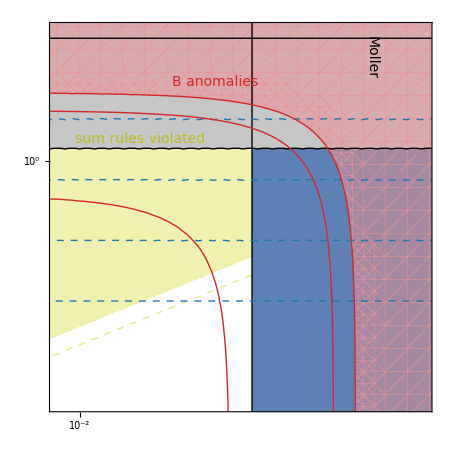

```mathematica
plotTR=Show[ptheoryPosPos1,ptheoryPosPos2,(*pMollerPosPos1,*)pZdecayPosPos1,psingletopPosPos1,praretopPosPos1,(*pMollerPosPos2,*)pBdecayPosPos1,(*pBdecayPosPos2,*)pZdecayPosPos2,psingletopPosPos2,praretopPosPos2,praretopPosPos3,pBdecayPosPos3,Evaluate[MyOptions],PlotRange->Log[{{0.007,2},{0.01,12}}]/Log[10],FrameTicks->{{myTicks2,None},{myTicks2,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"","","UV scalar dominated"},
Epilog->{Text[Style["B anomalies",FontFamily->MyFont,FontSize->14,MyDarkRed],{-1.1,.65},Automatic,{1,-0.05}],
Text[Style["Moller",FontFamily->MyFont,FontSize->14,Black],{-0.05,.85},Automatic,{0,-1}],
Text[Style["sum rules violated",FontFamily->MyFont,FontSize->14,MyDarkYellow],{-1.6,.18},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

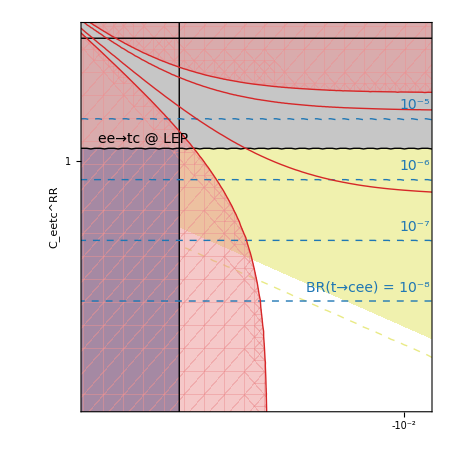

```mathematica
(*minCeettLR=NMinimize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pMollerNegPos2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerNegPos1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

minCeettRR=NMinimize[{C1,χ2[0,C1,0,0,0,C3,0,0,0,0,0,0,L]-minZdecay<4,minCeeccRR<C3<0},{C1,C3}][[1]];
pZdecayNegPos2=ContourPlot[C1==-Log[-minCeettRR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayNegPos1=RegionPlot[C1<-Log[-minCeettRR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayNegPos1=RegionPlot[chisqrBdecay[L,0,-10^-C1,0,10^C2,0,0,0,0]-minBdecayNeg>4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayNegPos2=RegionPlot[chisqrBdecay[L,0,-10^-C1,0,10^C2,0,0,0,0]-minBdecayNeg<1,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayNegPos3=ContourPlot[chisqrBdecay[L,0,-10^-C1,0,10^C2,0,0,0,0]-minBdecayNeg,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopNegPos2=ContourPlot[sigmaeetq[189^2][L,0,10^C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopNegPos1=RegionPlot[sigmaeetq[189^2][L,0,10^C2]>110,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[1]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopNegPos2=ContourPlot[BRtqll[L,0,10^C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.5]/Log[10],Log[20]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopNegPos1=RegionPlot[BRtqll[L,0,10^C2]>2.1*10^-4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopNegPos3=ContourPlot[BRtqll[L,0,10^C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryNegPos1=RegionPlot[10^C2>Sqrt[maxCeeccRR*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryNegPos2=ContourPlot[10^C2==Sqrt[maxCeeccRR/2*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,Log[0.005]/Log[10],Log[20]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotTL=Show[ptheoryNegPos1,ptheoryNegPos2,(*pMollerNegPos1,*)pZdecayNegPos1,psingletopNegPos1,praretopNegPos1,(*pMollerNegPos2,*)pBdecayNegPos1,(*pBdecayNegPos2,*)pZdecayNegPos2,psingletopNegPos2,praretopNegPos2,praretopNegPos3,pBdecayNegPos3,Evaluate[MyOptions],PlotRange->{-Log[{2,0.007}]/Log[10],Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicks1,None},{myTicksNegative2,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"","C_eetc^RR","UV vector dominated"},
Epilog->{Text[Style["BR(t→cee) = 10^-8",FontFamily->MyFont,FontSize->14,MyDarkBlue],{1.74,-1.04},Automatic,{1,0}],
Text[Style["10^-7",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-0.54},Automatic,{1,0}],
Text[Style["10^-6",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-.04},Automatic,{1,0}],
Text[Style["10^-5",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,.46},Automatic,{1,0}],
Text[Style["ee→tc @ LEP",FontFamily->MyFont,FontSize->14,Black],{.1,.18},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

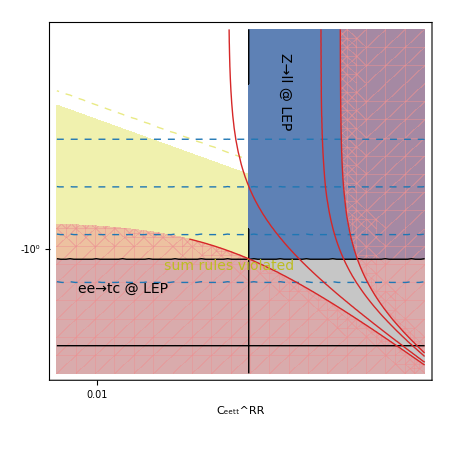

```mathematica
(*maxCeettLR=NMaximize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,0<C3<maxCeeccLR},{C1,C3}][[1]];
pMollerPosNeg2=ContourPlot[C1==Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerPosNeg1=RegionPlot[C1>Log[maxCeettLR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

maxCeettRR=NMaximize[{C1,χ2[0,C1,0,0,0,C3,0,0,0,0,0,0,L]-minZdecay<4,0<C3<maxCeeccRR},{C1,C3}][[1]];
pZdecayPosNeg2=ContourPlot[C1==Log[maxCeettRR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayPosNeg1=RegionPlot[C1>Log[maxCeettRR]/Log[10],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayPosNeg1=RegionPlot[chisqrBdecay[L,0,10^C1,0,-10^-C2,0,0,0,0]-minBdecayNeg>4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayPosNeg2=RegionPlot[chisqrBdecay[L,0,10^C1,0,-10^-C2,0,0,0,0]-minBdecayNeg<1,{C1,Log[0.05]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayPosNeg3=ContourPlot[chisqrBdecay[L,0,10^C1,0,-10^-C2,0,0,0,0]-minBdecayNeg,{C1,Log[0.05]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopPosNeg2=ContourPlot[sigmaeetq[189^2][L,0,-10^-C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopPosNeg1=RegionPlot[sigmaeetq[189^2][L,0,-10^-C2]>110,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopPosNeg2=ContourPlot[BRtqll[L,0,-10^-C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.5]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopPosNeg1=RegionPlot[BRtqll[L,0,-10^-C2]>2.1*10^-4,{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopPosNeg3=ContourPlot[BRtqll[L,0,-10^-C2],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]];

ptheoryPosNeg1=RegionPlot[10^-C2>Sqrt[maxCeeccRR*10^C1],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryPosNeg2=ContourPlot[10^-C2==Sqrt[maxCeeccRR/2*10^C1],{C1,Log[0.005]/Log[10],Log[3]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotBR=Show[ptheoryPosNeg1,ptheoryPosNeg2,(*pMollerPosNeg1,*)pZdecayPosNeg1,psingletopPosNeg1,praretopPosNeg1,(*pMollerPosNeg2,*)pBdecayPosNeg1,(*pBdecayPosNeg2,*)pZdecayPosNeg2,psingletopPosNeg2,praretopPosNeg2,praretopPosNeg3,pBdecayPosNeg3,Evaluate[MyOptions],PlotRange->{Log[{0.007,2}]/Log[10],-Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicksNegative2,None},{myTicks1,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"C_eett^RR","",""},
Epilog->{Text[Style["Z→ll @ LEP",FontFamily->MyFont,FontSize->14,Black],{-0.58,1.65},Automatic,{0,-1}],
Text[Style["sum rules violated",FontFamily->MyFont,FontSize->14,MyDarkYellow],{-1.,-.18},Automatic,{1,0}],
Text[Style["ee→tc @ LEP",FontFamily->MyFont,FontSize->14,Black],{-1.8,-.42},Automatic,{1,0}]}]
```

Lighter::arg: Grey should be a valid color directive, an image, or a list of them.

Lighter::arg: Lighter[Grey] should be a valid color directive, an image, or a list of them.

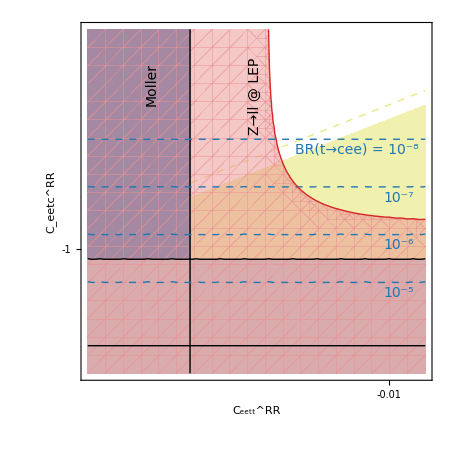

```mathematica
(*minCeettLR=NMinimize[{C1,deltaAoverAMoller[L,C1,0,C3,0,0,0]^2/0.024^2<4,minCeeccLR<C3<0},{C1,C3}][[1]];
pMollerNegNeg2=ContourPlot[C1==-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thin]];
pMollerNegNeg1=RegionPlot[C1<-Log[-minCeettLR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];*)

minCeettRR=NMinimize[{C1,χ2[0,C1,0,0,0,C3,0,0,0,0,0,0,L]-minZdecay<4,minCeeccRR<C3<0},{C1,C3}][[1]];
pZdecayNegNeg2=ContourPlot[C1==-Log[-minCeettRR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[Black,Thick]];
pZdecayNegNeg1=RegionPlot[C1<-Log[-minCeettRR]/Log[10],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Grey]];

pBdecayNegNeg1=RegionPlot[chisqrBdecay[L,0,-10^-C1,0,-10^-C2,0,0,0,0]-minBdecayNeg>4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed,Opacity[0.5]]];
pBdecayNegNeg2=RegionPlot[chisqrBdecay[L,0,-10^-C1,0,-10^-C2,0,0,0,0]-minBdecayNeg<1,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyRed]];
pBdecayNegNeg3=ContourPlot[chisqrBdecay[L,0,-10^-C1,0,-10^-C2,0,0,0,0]-minBdecayNeg,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{1,4},ContourShading->None,ContourStyle->MyDarkRed];

psingletopNegNeg2=ContourPlot[sigmaeetq[189^2][L,0,-10^-C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{110},ContourShading->None,ContourStyle->Directive[Black,Thick]];
psingletopNegNeg1=RegionPlot[sigmaeetq[189^2][L,0,-10^-C2]>110,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];

praretopNegNeg2=ContourPlot[BRtqll[L,0,-10^-C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.5]/Log[10]},Contours->{2.1*10^-4},ContourShading->None,ContourStyle->Directive[Black,Thin]];
praretopNegNeg1=RegionPlot[BRtqll[L,0,-10^-C2]>2.1*10^-4,{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[Lighter@Lighter@Gray]];
praretopNegNeg3=ContourPlot[BRtqll[L,0,-10^-C2],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},Contours->{10^-8,10^-7,10^-6,10^-5},ContourShading->None,ContourStyle->Directive[MyDarkBlue,Dashed,Thick]]; 

ptheoryNegNeg1=RegionPlot[10^-C2>Sqrt[maxCeeccRR*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},BoundaryStyle->None,PlotStyle->Directive[MyYellow//Lighter]];
ptheoryNegNeg2=ContourPlot[10^-C2==Sqrt[maxCeeccRR/2*10^-C1],{C1,-Log[3]/Log[10],-Log[0.005]/Log[10]},{C2,-Log[20]/Log[10],-Log[0.005]/Log[10]},ContourShading->None,ContourStyle->Directive[MyYellow,Dashed,Thick]];

plotBL=Show[ptheoryNegNeg1,ptheoryNegNeg2,(*pMollerNegNeg1,*)pZdecayNegNeg1,psingletopNegNeg1,praretopNegNeg1,(*pMollerNegNeg2,*)pBdecayNegNeg1,(*pBdecayNegNeg2,*)pZdecayNegNeg2,psingletopNegNeg2,praretopNegNeg2,praretopNegNeg3,pBdecayNegNeg3,Evaluate[MyOptions],PlotRange->{-Log[{2,0.007}]/Log[10],-Log[{0.01,12}]/Log[10]},FrameTicks->{{myTicksNegative1,None},{myTicksNegative1,None}},ImageSize->450,ImagePadding->{{90,20},{80,40}},FrameLabel->{"C_eett^RR","C_eetc^RR",""},
Epilog->{Text[Style["BR(t→cee) = 10^-8",FontFamily->MyFont,FontSize->14,MyDarkBlue],{1.74,1.04},Automatic,{1,0}],
Text[Style["10^-7",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,0.54},Automatic,{1,0}],
Text[Style["10^-6",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,.04},Automatic,{1,0}],
Text[Style["10^-5",FontFamily->MyFont,FontSize->14,MyDarkBlue],{2.08,-.46},Automatic,{1,0}],
Text[Style["Z→ll @ LEP",FontFamily->MyFont,FontSize->14,Black],{0.9,1.6},Automatic,{0,1}],
Text[Style["Moller",FontFamily->MyFont,FontSize->14,Black],{0.05,1.72},Automatic,{0,1}]}]
```

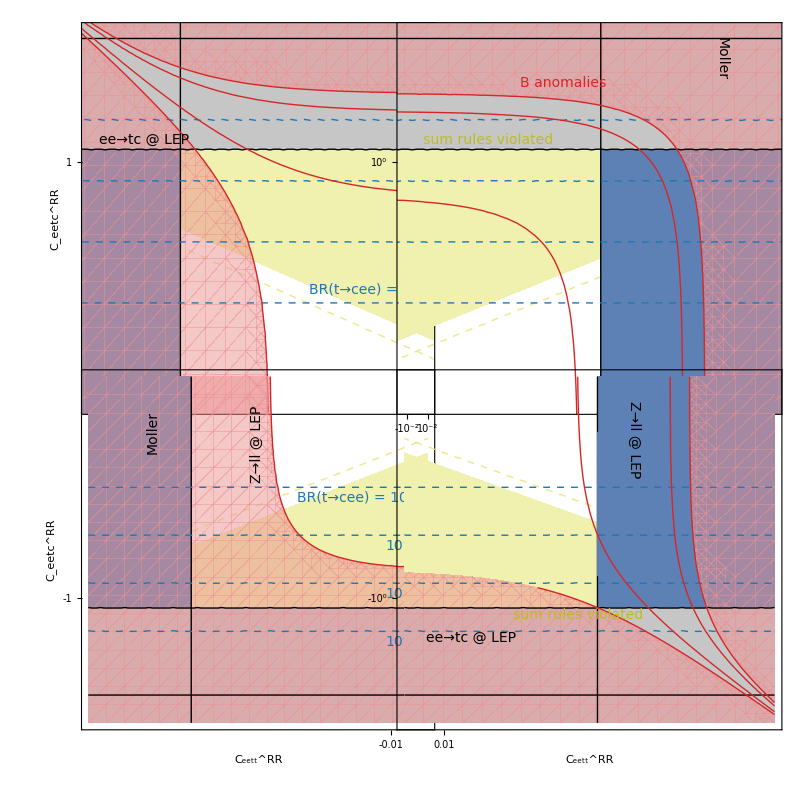

```mathematica
finalBeetcRR=GraphicsGrid[{{plotTL,plotTR},{plotBL,plotBR}},Spacings->{-105,-105},Frame->None,ImageSize->800]
```

## Branching Ratio Functions

```mathematica
(*Coefficient Constraint Function*)
Cmnpq[Cmmpp_,Cmmqq_,Cnnpp_,Cnnqq_]:=Sqrt[Cmmpp*Cnnqq]+Sqrt[Cmmqq*Cnnpp]+4*(Cmmpp*Cmmqq*Cnnpp*Cnnqq)^(.25);
Cmnpq$F1[Cmmpp_,Cmmqq_,Cnnpp_,Cnnqq_]:=Sqrt[Cmmpp*Cnnqq]+Sqrt[Cmmqq*Cnnpp];
Cmmpq[Cmmpp_,Cmmqq_]:=Sqrt[Cmmpp*Cmmqq];
(*Branching Ratio Functions*)
v=246*10^(-3);
mt=162.92*10^(-3);
mt$2=172.76*10^(-3 );
mw=80.377*10^(-3);
BR[CmmppLR_,CmmqqLR_,CnnppLR_,CnnqqLR_,CmmppRR_,CmmqqRR_,CnnppRR_,CnnqqRR_]:=(mt^2*v^2)/(96*Pi^2)*(Cmnpq[CmmppLR,CmmqqLR,CnnppLR,CnnqqLR]^2+Cmnpq[CmmppRR,CmmqqRR,CnnppRR,CnnqqRR]^2)(1-mw^2/mt^2)^(-2)*(1+(2*mw^2)/mt^2)^(-1);(*eq 13*)
BR$nofac[CmmppLR_,CmmqqLR_,CnnppLR_,CnnqqLR_,CmmppRR_,CmmqqRR_,CnnppRR_,CnnqqRR_]:=(Cmnpq[CmmppLR,CmmqqLR,CnnppLR,CnnqqLR]^2+Cmnpq[CmmppRR,CmmqqRR,CnnppRR,CnnqqRR]^2);
BR$nofac$F1[CmmppLR_,CmmqqLR_,CnnppLR_,CnnqqLR_,CmmppRR_,CmmqqRR_,CnnppRR_,CnnqqRR_]:=(Cmnpq$F1[CmmppLR,CmmqqLR,CnnppLR,CnnqqLR]^2+Cmnpq$F1[CmmppRR,CmmqqRR,CnnppRR,CnnqqRR]^2);
BRfac=(mt^2*v^2)/(96*Pi^2)*(1-mw^2/mt^2)^(-2)*(1+(2*mw^2)/mt^2)^(-1);
BRF1$nofac[CmmppLR_,CmmqqLR_,CmmppRR_,CmmqqRR_]:=(Cmmpq[CmmppLR,CmmqqLR]^2+Cmmpq[CmmppRR,CmmqqRR]^2);
```

```mathematica
BReectF1LR=ScientificForm[BRfac*NMaximize[{BRF1$nofac[CeeccLR,CeettLR,0,0],minCeeccLR<CeeccLR<maxCeeccLR,minCeettLR<CeettLR<maxCeettLR},{CeeccLR,CeettLR}][[1]]]
```

1.3157×10^-7

```mathematica
BReectF1LR=ScientificForm[BRfac*NMaximize[{BRF1$nofac[CeeccLR,CeettLR,0,0],minCeeccLR<CeeccLR<maxCeeccLR,minCeettLR<CeettLR<maxCeettLR,chisqrBdecay[1000,CeettLR,0,Cmmpq[CeeccLR,CeettLR],0,0,0,0,0]-minBdecayPos<4},{CeeccLR,CeettLR}][[1]]]
```

1.26696×10^-10

```mathematica
BReectF1RR=ScientificForm[BRfac*NMaximize[{BRF1$nofac[0, 0, CeeccLR,CeettLR],minCeeccLR<CeeccLR<maxCeeccLR,minCeettLR<CeettLR<maxCeettLR},{CeeccLR,CeettLR}][[1]]]
```

```mathematica
BReectF1RR=ScientificForm[BRfac*NMaximize[{BRF1$nofac[0, 0, CeeccLR,CeettLR],minCeeccLR<CeeccLR<maxCeeccLR,minCeettLR<CeettLR<maxCeettLR,chisqrBdecay[1000,CeettLR,0,Cmmpq[CeeccLR,CeettLR],0,0,0,0,0]-minBdecayPos<4},{CeeccLR,CeettLR}][[1]]]
```